```mathematica
GammaConnection[coord_List,Metric_List]:=Block[{n,InverseMetric,t,ChristoffelSymbols,listChristoffelSymbols,iind,jind,kind,lind,gamma,racciM},
n=Length[coord];
InverseMetric=Simplify[Inverse[Metric]];
ChristoffelSymbols=Table[1/2*Sum[(InverseMetric[[kind,lind]])*(D[Metric[[jind,lind]],coord[[iind]]]+D[Metric[[iind,lind]],coord[[jind]]]-D[Metric[[iind,jind]],coord[[lind]]]),{lind,1,n}],{kind,1,n},{iind,1,n},{jind,1,n}]
]
Racci[gamma_,mu_,sig_,co_]:=Sum[D[gamma[nu,mu,sig],co[[nu]]],{nu,1,Length[co]}]-Sum[D[gamma[nu,nu,sig],co[[mu]]],{nu,1,Length[co]}]+Sum[gamma[la,mu,sig]gamma[nu,la,nu],{nu,1,Length[co]},{la,1,Length[co]}]-Sum[gamma[la,nu,sig]gamma[nu,la,mu],{nu,1,Length[co]},{la,1,Length[co]}]
racciCurFromMetric[coord_List,Metric_List]:=Block[{n,InverseMetric,t,ChristoffelSymbols,listChristoffelSymbols,iind,jind,kind,lind,gamma,racciM},
n=Length[coord];
InverseMetric=Simplify[Inverse[Metric]];
ChristoffelSymbols=GammaConnection[coord,Metric];
Do[gamma[kind,iind,jind]=ChristoffelSymbols[[kind,iind,jind]],{kind,1,n},{iind,1,n},{jind,1,n}];
racciM=Table[Racci[gamma,mu,sig,coord],{mu,1,n},{sig,1,n}];
racciM
]
(*Subscript[R, abc]^d*)
riemannTensorFromMetric[coord_List,Metric_List]:=Block[{n,InverseMetric,t,ChristoffelSymbols,iind,jind,kind,lind,inda,indb,indc,indd,riemann},
n=Length[coord];
InverseMetric=Simplify[Inverse[Metric]];
ChristoffelSymbols=Simplify[Table[1/2*Sum[(InverseMetric[[kind,lind]])*(D[Metric[[jind,lind]],coord[[iind]]]+D[Metric[[iind,lind]],coord[[jind]]]-D[Metric[[iind,jind]],coord[[lind]]]),{lind,1,n}],{kind,1,n},{iind,1,n},{jind,1,n}]];
riemann=Table[-D[ChristoffelSymbols[[indd,indb,indc]],coord[[inda]]]+D[ChristoffelSymbols[[indd,inda,indc]],coord[[indb]]]+Sum[
ChristoffelSymbols[[inde,indc,inda]]ChristoffelSymbols[[indd,indb,inde]],{inde,1,n} ]-Sum[
ChristoffelSymbols[[inde,indc,indb]]ChristoffelSymbols[[indd,inda,inde]],{inde,1,n} ],{inda,1,n},{indb,1,n},{indc,1,n},{indd,1,n}
]
]
extrinsicCur[gmetric_,coorList_,conormal_,spaceTimeLike_]:=Block[{ginv,christoffelSymbols,normalizedConorm,h3metric,projection,extrinsicK},
ginv=Inverse[gmetric];
christoffelSymbols=GammaConnection[coorList,gmetric];
normalizedConorm=conormal/√(spaceTimeLike conormal.ginv.conormal);
h3metric=gmetric-spaceTimeLike TensorProduct[normalizedConorm,normalizedConorm];
projection=h3metric.ginv;
extrinsicK=projection.(D[normalizedConorm,{coorList}]-normalizedConorm.christoffelSymbols).Transpose[projection]
]
funD[f_,k_[x_]]:=Block[{order},
order=Cases[f,Derivative[_][k][x],Infinity]//DeleteDuplicates;
order=order/.Derivative[n_][k][x]:>n;
D[f,k[x]]+Total[Map[(-1)^# D[D[f,Derivative[#][k][x]],{x,#}]&,order]]
]
(*canonicalPairs should be {{{x1,p1},(the valur of [x1,p1])},...}*)
poissonFun[{f1_,f2_},canonicalPairs_]:=(#[[2]](funD[f1,#[[1,1]]]funD[f2,#[[1,2]]]-funD[f2,#[[1,1]]]funD[f1,#[[1,2]]])&/@canonicalPairs)//Total
lieDerivative[vector_,tensor_,type_,coor_]/;type=={0,0}:=D[tensor,{coor}].vector
(*here a tensor with the type (m,n) should be input as tensor[[a1,a2,...,am,b1,...,bn]]*)
lieDerivative[vector_,tensor_,type_,coor_]/;type=!={0,0}:=Block[{term1,term2,term3,contractingIndex,resortIndex},
term1=D[tensor,{coor}].vector;
contractingIndex=Insert[Range[2,Total[type]],1,#]&/@Range[Total[type]];
resortIndex=TakeDrop[Range[Total[type]],{#}]&/@Range[Total[type]];
resortIndex=Flatten/@resortIndex;
term2=If[type[[1]]==0,0,(D[vector,{coor}].Transpose[tensor,#])&/@contractingIndex[[Range[type[[1]]]]]];
term2=If[type[[1]]==0,0,MapThread[Transpose[#1,#2]&,{term2,resortIndex[[Range[type[[1]]]]]}]];
term2=-term2//Total;
term3=If[type[[2]]==0,0,(Transpose[D[vector,{coor}]].Transpose[tensor,#])&/@contractingIndex[[Range[type[[1]]+1,Total[type]] ]]];
term3=If[type[[2]]==0,0,MapThread[Transpose[#1,#2]&,{term3,resortIndex[[ Range[type[[1]]+1,Total[type]] ]]}]];
term3=term3//Total;
term1+term2+term3
]
findScalars[variablesWithWeight_]:=Block[{variablesWithWeightp,allVariables,density1pairs,newScalars},
variablesWithWeightp=If[#[[2]]==0,{#,D[#[[1]],x]->1},#]&/@variablesWithWeight//Flatten;
allVariables=Reverse/@variablesWithWeightp;
allVariables=GroupBy[allVariables,Keys,Last/@#&];
density1pairs=Subsets[allVariables[1],{2}];
density1pairs=DeleteCases[density1pairs,_?(AllTrue[#, MemberQ[#,Derivative,Infinity,Heads->True]&]&)];
density1pairs=SortBy[#,!MemberQ[#,Derivative,Infinity,Heads->True]&]&/@density1pairs;
newScalars=#[[1]]/#[[2]]&/@density1pairs;
newScalars=newScalars->0//Thread;
{variablesWithWeightp,newScalars}//DeleteDuplicates//Flatten
]
```

```mathematica
HvGau=-(K1[x] E1'[x]-2 E2[x] K2'[x])/(2 G);
HScal=(-8 E1[x] E2[x]^2 K1[x] K2[x]-4 E2[x]^3 (1+K2[x]^2)-4 E1[x] E1'[x] E2'[x]+E2[x] (E1'[x]^2+4 E1[x] E1''[x]))/(8 G √E1[x] E2[x]^2);
canonicalPairs={{{K1[x],E1[x]},2G},{{K2[x],E2[x]},G}};
```

```mathematica
arealGF1=E1->Function[x,x^2];
arealGF2=Solve[0==HvGau/.arealGF1,K1[x]]//First;
arealGF2=K1->Function[x,Evaluate[K1[x]/.arealGF2]];
arealGF={arealGF1,arealGF2}//Flatten
```

{E1→Function[x,x^2],K1→Function[x,(E2[x] K2'[x])/x]}

```mathematica
allVariables={E1[x],E2[x],K1[x],K2[x]};
allVariables=allVariables->{0,1,1,0}//Thread
```

{E1[x]→0,E2[x]→1,K1[x]→1,K2[x]→0}

```mathematica
allScalars=Nest[findScalars,allVariables,3];
allScalars=GroupBy[allScalars,Values,Keys];
allScalars=allScalars[0]//FullSimplify//DeleteDuplicates;
allScalars=DeleteCases[allScalars,_?(MemberQ[#,Derivative[_][f_][x]/;MemberQ[{K1,K2},f],Infinity]&)];
allScalars=DeleteCases[allScalars,_?(MemberQ[#,Derivative[n_][_][x]/;n≥3,Infinity]&)];
allScalars=allScalars/.E2[x]/K1[x]->K1[x]/E2[x];
allScalars=allScalars->{1,2,4,5,3,6,7}//Thread;
allScalars=SortBy[allScalars,Last]//Keys
```

{E1[x],K2[x],K1[x]/E2[x],E1'[x]/E2[x],E1'[x]/K1[x],(-E1'[x] E2'[x]+E2[x] E1''[x])/E2[x]^3,(-E1'[x] E2'[x]+E2[x] E1''[x])/(E2[x]^2 K1[x])}

```mathematica
Hv1=Nx[x]HvGau;
```

```mathematica
poissonHvScalars=Expand[poissonFun[{Smear[x]#,Hv1},canonicalPairs]]&/@allScalars;
poissonHvScalars=poissonHvScalars+(D[Nx[x]Smear[x],x]allScalars)//Expand;
poissonHvScalars=Integrate[#,x]&/@poissonHvScalars;
AllTrue[Head/@poissonHvScalars,#=!=Integrate&]
```

True

```mathematica
selfPoisson={N1[x]#,N2[x]#}&/@allScalars;
selfPoisson=poissonFun[{#[[1]],#[[2]]},canonicalPairs]&/@selfPoisson//Expand;
selfPoisson=selfPoisson/.Times[a___,Derivative[n_][f_][x]/;MemberQ[{N1,N2},f]&&n≥2]:>-D[Times[a],x]D[f[x],x]//Expand;
selfPoissonByNpN=selfPoisson/(N2[x] N1'[x]-N1[x] N2'[x])//Simplify//Expand
```

{0,0,0,0,-(2 G E1'[x])/K1[x]^3,0,-(4 G E1'[x] E2'[x]^2)/(E2[x]^4 K1[x]^3)-(2 G E1'[x] E2'[x] K1'[x])/(E2[x]^3 K1[x]^4)+(4 G E2'[x] E1''[x])/(E2[x]^3 K1[x]^3)+(2 G K1'[x] E1''[x])/(E2[x]^2 K1[x]^4)+(2 G E1'[x] E2''[x])/(E2[x]^3 K1[x]^3)-(2 G E1^(3)[x])/(E2[x]^2 K1[x]^3)}

```mathematica
scalar8=1/E2[x] D[allScalars[[-2]],x]//Simplify;
p1=poissonFun[{N1[x]scalar8,N2[x]allScalars[[3]]},canonicalPairs]//Expand
p2=poissonFun[{N2[x]scalar8,N1[x]allScalars[[3]]},canonicalPairs]//Expand
p1-p2/.Times[a___,Derivative[n_][f_][x]/;MemberQ[{N1,N2},f]&&n≥2]:>(-1)^(n-1)D[Times[a],{x,n-1}]D[f[x],x]//Expand
%/.Times[a___,Derivative[n_][f_][x]/;MemberQ[{N1,N2},f]&&n≥2]:>(-1)^(n-1)D[Times[a],{x,n-1}]D[f[x],x]//Expand
```

-(30 G N1[x] N2[x] E2'[x]^3)/E2[x]^7+(30 G N2[x] E2'[x]^2 N1'[x])/E2[x]^6+(20 G N1[x] N2[x] E2'[x] E2''[x])/E2[x]^6-(8 G N2[x] N1'[x] E2''[x])/E2[x]^5-(12 G N2[x] E2'[x] N1''[x])/E2[x]^5-(2 G N1[x] N2[x] E2^(3)[x])/E2[x]^5+(2 G N2[x] N1^(3)[x])/E2[x]^4

-(30 G N1[x] N2[x] E2'[x]^3)/E2[x]^7+(30 G N1[x] E2'[x]^2 N2'[x])/E2[x]^6+(20 G N1[x] N2[x] E2'[x] E2''[x])/E2[x]^6-(8 G N1[x] N2'[x] E2''[x])/E2[x]^5-(12 G N1[x] E2'[x] N2''[x])/E2[x]^5-(2 G N1[x] N2[x] E2^(3)[x])/E2[x]^5+(2 G N1[x] N2^(3)[x])/E2[x]^4

(10 G N2[x] E2'[x]^2 N1'[x])/E2[x]^6-(10 G N1[x] E2'[x]^2 N2'[x])/E2[x]^6-(4 G N2[x] N1'[x] E2''[x])/E2[x]^5+(4 G N1[x] N2'[x] E2''[x])/E2[x]^5-(2 G N2'[x] N1''[x])/E2[x]^4+(2 G N1'[x] N2''[x])/E2[x]^4

(10 G N2[x] E2'[x]^2 N1'[x])/E2[x]^6-(10 G N1[x] E2'[x]^2 N2'[x])/E2[x]^6-(4 G N2[x] N1'[x] E2''[x])/E2[x]^5+(4 G N1[x] N2'[x] E2''[x])/E2[x]^5-(2 G N2'[x] N1''[x])/E2[x]^4+(2 G N1'[x] N2''[x])/E2[x]^4

```mathematica
selfPoissonTerms=poissonFun[{N1[x]E2[x]F[Other[x],allScalars[[7]]],N2[x]E2[x]F[Other[x],allScalars[[7]]]},canonicalPairs]//Expand;
selfPoissonTerms=selfPoissonTerms/.Times[a___,Derivative[n_][f_][x]/;MemberQ[{N1,N2},f]&&n≥2]:>-D[Times[a],x]D[f[x],x]//Expand;
selfPoissonTerms=selfPoissonTerms/(2 G (N1[x] N2'[x]-N2[x] N1'[x]))//Simplify//Expand;
selfPoissonTerms==1/K1[x]^2 E2[x]D[allScalars[[7]],x](Derivative[0,1][F][Other[x],(-E1'[x] E2'[x]+E2[x] E1''[x])/(E2[x]^2 K1[x])])^2//Expand
```

True

```mathematica
selfPoissonTerms=poissonFun[{N1[x]E2[x]F[allScalars[[5]],Other[x]],N2[x]E2[x]F[allScalars[[5]],Other[x]]},canonicalPairs]//Simplify;
selfPoissonTerms=selfPoissonTerms/(2 G (N1[x] N2'[x]-N2[x] N1'[x]))//Simplify//Expand
selfPoissonTerms==(E2[x]^2 allScalars[[5]])/K1[x]^2(Derivative[1,0][F][allScalars[[5]],Other[x]])^2
```

(E2[x]^2 E1'[x] (F^(1,0)[E1'[x]/K1[x],Other[x]])^2)/K1[x]^3

True

```mathematica
scalarPairs1=Table[{N1[x]extraTerm[a,x]allScalars[[a]],N2[x]extraTerm[b,x]allScalars[[b]]},{a,1,7},{b,1,7}];
poissonPair1=Map[poissonFun[{#[[1]],#[[2]]},canonicalPairs]&,scalarPairs1,{2}]//Simplify;
Print["terms not propotional to delta(x,y)"]
Sort/@Position[poissonPair1,HoldPattern[Times[___,N1[x],___,N2[x],___]|0],{2}]//DeleteDuplicates//DeleteCases[#,{i_,i_}]&
scalarPairs2=Table[{N2[x]extraTerm[a,x]allScalars[[a]],N1[x]extraTerm[b,x]allScalars[[b]]},{a,1,7},{b,1,7}];
poissonPair2=Map[poissonFun[{#[[1]],#[[2]]},canonicalPairs]&,scalarPairs2,{2}]//Expand;
poissonPair=poissonPair1-poissonPair2//Expand;
(poissonPair=ReplacePart[poissonPair,{i_,i_}:>0]//FullSimplify//Expand)//MatrixForm;
poissonPair=poissonPair/.Times[a___,Derivative[2][f_][x]/;MemberQ[{N1,N2},f]]:>-D[Times[a],x]D[f[x],x];
poissonPair=poissonPair/.extraTerm:>Function[{a,x},E2[x]Derivative[0,1][F][other[x],s[a,x]]];
(poissonPair=poissonPair/(2 G (N1[x] N2'[x]-N2[x] N1'[x]))//Simplify);
vanishingTerms=Sort/@DeleteCases[Position[poissonPair,0,{2}],{i_,i_}]//DeleteDuplicates
nonVanishingTerms=Sort/@Position[poissonPair,_?(#=!=0&),{2},Heads->False]//DeleteDuplicates
DeleteCases[nonVanishingTerms,{_,5|7}|{5|7,_}]
```

terms not propotional to delta(x,y)

{{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{2,3},{2,4},{2,5},{4,6}}

{{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{2,3},{2,4},{2,5},{4,6}}

{{2,6},{2,7},{3,4},{3,5},{3,6},{3,7},{4,5},{4,7},{5,6},{5,7},{6,7}}

{{2,6},{3,4},{3,6}}

```mathematica
poissonPair[[2,6]]
poissonPair[[2,7]]
poissonPair[[3,4]]
poissonPair[[3,5]]
```

(E1'[x] F^(0,1)[other[x],s[2,x]] F^(0,1)[other[x],s[6,x]])/(2 E2[x])

(E1'[x] F^(0,1)[other[x],s[2,x]] F^(0,1)[other[x],s[7,x]])/(2 K1[x])

-F^(0,1)[other[x],s[3,x]] F^(0,1)[other[x],s[4,x]]

-(E2[x] F^(0,1)[other[x],s[3,x]] F^(0,1)[other[x],s[5,x]])/K1[x]

```mathematica
poissonPair[[3,6]]==1/E2[x](Derivative[0,1][F][other[x],s[3,x]]D[Derivative[0,1][F][other[x],s[6,x]],x]-D[Derivative[0,1][F][other[x],s[3,x]],x]Derivative[0,1][F][other[x],s[6,x]])
```

True

```mathematica
poissonPair[[3,7]]==Derivative[0,1][F][other[x],s[3,x]] D[(Derivative[0,1][F][other[x],s[7,x]])/K1[x],x]-(E2[x]Derivative[0,1][F][other[x],s[7,x]])/K1[x] D[1/E2[x] Derivative[0,1][F][other[x],s[3,x]],x]//Expand
```

True

```mathematica
poissonPair[[4,5]]
```

(E2[x] E1'[x] F^(0,1)[other[x],s[4,x]] F^(0,1)[other[x],s[5,x]])/K1[x]^2

```mathematica
poissonPair[[4,7]]==Derivative[0,1][F][other[x],s[4,x]]Derivative[0,1][F][other[x],s[7,x]]D[D[E1[x],x]/E2[x],x] E2[x]/K1[x]^2//Expand
```

True

```mathematica
poissonPair[[5,6]]==(Derivative[0,1][F][other[x],s[5,x]] Derivative[0,1][F][other[x],s[6,x]]D[D[E1[x],x]/K1[x]^2,x]-(E2[x]D[E1[x],x])/K1[x]^2 Derivative[0,1][F][other[x],s[5,x]]D[1/E2[x] Derivative[0,1][F][other[x],s[6,x]],x]+E1'[x]/K1[x]^2 Derivative[0,1][F][other[x],s[6,x]]D[Derivative[0,1][F][other[x],s[5,x]],x])//Expand
```

True

```mathematica
poissonPair[[5,7]]==(Derivative[0,1][F][other[x],s[5,x]]Derivative[0,1][F][other[x],s[7,x]] E2[x]/K1[x]^2 D[D[E1[x],x]/K1[x],x]+(E2[x] Derivative[0,1][F][other[x],s[7,x]])/K1[x]^2 D[D[E1[x],x]/K1[x] Derivative[0,1][F][other[x],s[5,x]],x]-(E1'[x] Derivative[0,1][F][other[x],s[5,x]])/K1[x]^2 D[E2[x]/K1[x] Derivative[0,1][F][other[x],s[7,x]],x])//Expand
```

True

```mathematica
poissonPair[[6,7]]==(Derivative[0,1][F][other[x],s[6,x]] Derivative[0,1][F][other[x],s[7,x]] 1/E2[x] D[(E2[x]E1''[x]-E2'[x]E1'[x])/(E2[x] K1[x]^2),x]+Derivative[0,1][F][other[x],s[7,x]](E1'[x] E2'[x]-E1''[x] E2[x])/(K1[x]^2 E2[x]^2)D[ Derivative[0,1][F][other[x],s[6,x]],x]-(E1'[x] E2'[x]-E1''[x]E2[x])/(E2[x]^2 K1[x]^2) Derivative[0,1][F][other[x],s[6,x]]D[ Derivative[0,1][F][other[x],s[7,x]],x])//Expand
```

True

```mathematica
allScalars4H=Most[allScalars]//Drop[#,{5}]&
```

{E1[x],K2[x],K1[x]/E2[x],E1'[x]/E2[x],(-E1'[x] E2'[x]+E2[x] E1''[x])/E2[x]^3}

```mathematica
sRule={s1,s2,s3,s4,s6}->allScalars4H//Thread
```

{s1→E1[x],s2→K2[x],s3→K1[x]/E2[x],s4→E1'[x]/E2[x],s6→(-E1'[x] E2'[x]+E2[x] E1''[x])/E2[x]^3}

```mathematica
eqs4M[M_]:=D[M,s2]D[M,s2,s4]-D[M,s4]D[M,{s2,2}]
HeffFromM[M_]:=-2E2[x](D[M,s1]+D[M,s2]/2 s3+D[M,s4]/s4 s6)/.sRule
```

## Variation of μ and its Lie derivative

```mathematica
sRule={s1,s2,s3,s4,s5,s6,s7}->allScalars//Thread
```

{s1→E1[x],s2→K2[x],s3→K1[x]/E2[x],s4→E1'[x]/E2[x],s5→E1'[x]/K1[x],s6→(-E1'[x] E2'[x]+E2[x] E1''[x])/E2[x]^3,s7→(-E1'[x] E2'[x]+E2[x] E1''[x])/(E2[x]^2 K1[x])}

```mathematica
checkPoisson[sa_,sb_,sRule_]:=Block[{funs1,funs2,result1,result2},funs1=λ1[x]sa/.sRule;
funs2=λ2[x]sb/.sRule;
result1=(poissonFun[{funs1,α[x]funs2},canonicalPairs]//Expand)/.Times[Derivative[n_][λ1][x],b__]:>(-1)^n λ1[x]D[Times[b],{x,n}];
result2=(poissonFun[{funs1,funs2},canonicalPairs]//Expand)/.Times[Derivative[n_][λ1][x],b__]:>(-1)^n λ1[x]D[Times[b],{x,n}];
{sa,sb}->(result1-α[x]result2/.{λ1[x]->μ[sa][x],λ2[x]->E2[x]NN[x]F[sb][x]})//Expand
]
```

```mathematica
checkPoisson[s1,#,sRule]&/@{s1,s2,s3,s4,s6}
checkPoisson[s2,#,sRule]&/@{s1,s2,s3,s4,s6}
checkPoisson[s3,#,sRule]&/@{s1,s2,s3,s4,s6}
checkPoisson[s4,#,sRule]&/@{s1,s2,s3,s4,s6}
checkPoisson[s6,#,sRule]&/@{s1,s2,s3,s4,s6}
```

{{s1,s1}→0,{s1,s2}→0,{s1,s3}→0,{s1,s4}→0,{s1,s6}→0}

{{s2,s1}→0,{s2,s2}→0,{s2,s3}→0,{s2,s4}→0,{s2,s6}→(G NN[x] F[s6][x] μ[s2][x] E1'[x] α'[x])/E2[x]^2}

{{s3,s1}→0,{s3,s2}→0,{s3,s3}→0,{s3,s4}→-(2 G NN[x] F[s4][x] μ[s3][x] α'[x])/E2[x],{s3,s6}→-(6 G NN[x] F[s6][x] μ[s3][x] E2'[x] α'[x])/E2[x]^3+(4 G μ[s3][x] α'[x] λ2'[x])/E2[x]^3+(2 G NN[x] F[s6][x] μ[s3][x] α''[x])/E2[x]^2}

{{s4,s1}→0,{s4,s2}→0,{s4,s3}→-(2 G NN[x] F[s3][x] μ[s4][x] α'[x])/E2[x],{s4,s4}→0,{s4,s6}→0}

{{s6,s1}→0,{s6,s2}→(G NN[x] F[s2][x] μ[s6][x] E1'[x] α'[x])/E2[x]^2,{s6,s3}→(6 G NN[x] F[s3][x] μ[s6][x] E2'[x] α'[x])/E2[x]^3-(4 G μ[s6][x] α'[x] λ2'[x])/E2[x]^3-(2 G NN[x] F[s3][x] μ[s6][x] α''[x])/E2[x]^2,{s6,s4}→0,{s6,s6}→0}

```mathematica
F=X[s1,s2,s4,s3+C1[s1,s2,s4]s6];
μ=(2 G^2)/s1 D[F,s3]^2 D[C1[s1,s2,s4],s2]
```

(2 G^2 C1^(0,1,0)[s1,s2,s4] (X^(0,0,0,1)[s1,s2,s4,s3+s6 C1[s1,s2,s4]])^2)/s1

```mathematica
eq=1/2 D[F,s2]D[F,s6]s4-D[F,s3]D[F,s4]+(D[F,s1,s6]D[F,s3]-D[F,s6]D[F,s1,s3])s4+(D[F,s4,s6]D[F,s3]-D[F,s6]D[F,s4,s3])s6+(μ s1 s3 s4)/(4 G^2)//Expand
```

1/2 s3 s4 C1^(0,1,0)[s1,s2,s4] (X^(0,0,0,1)[s1,s2,s4,s3+s6 C1[s1,s2,s4]])^2+1/2 s4 s6 C1[s1,s2,s4] C1^(0,1,0)[s1,s2,s4] (X^(0,0,0,1)[s1,s2,s4,s3+s6 C1[s1,s2,s4]])^2+s4 C1^(1,0,0)[s1,s2,s4] (X^(0,0,0,1)[s1,s2,s4,s3+s6 C1[s1,s2,s4]])^2-X^(0,0,0,1)[s1,s2,s4,s3+s6 C1[s1,s2,s4]] X^(0,0,1,0)[s1,s2,s4,s3+s6 C1[s1,s2,s4]]+1/2 s4 C1[s1,s2,s4] X^(0,0,0,1)[s1,s2,s4,s3+s6 C1[s1,s2,s4]] X^(0,1,0,0)[s1,s2,s4,s3+s6 C1[s1,s2,s4]]

```mathematica
eq2=D[μ,s2]D[F,s6]s4-2D[μ,s3]D[F,s4]-2D[μ,s4]D[F,s3]+4(D[μ,s3]D[F,s6,s1]-D[μ,s6]D[F,s3,s1])s4+4(D[μ,s3]D[F,s6,s4]-D[μ,s6]D[F,s3,s4])s6//Expand
```

-(4 G^2 C1^(0,1,1)[s1,s2,s4] (X^(0,0,0,1)[s1,s2,s4,s3+s6 C1[s1,s2,s4]])^3)/s1+(2 G^2 s4 C1[s1,s2,s4] C1^(0,2,0)[s1,s2,s4] (X^(0,0,0,1)[s1,s2,s4,s3+s6 C1[s1,s2,s4]])^3)/s1+(4 G^2 s4 s6 C1[s1,s2,s4] (C1^(0,1,0)[s1,s2,s4])^2 (X^(0,0,0,1)[s1,s2,s4,s3+s6 C1[s1,s2,s4]])^2 X^(0,0,0,2)[s1,s2,s4,s3+s6 C1[s1,s2,s4]])/s1+(16 G^2 s4 C1^(0,1,0)[s1,s2,s4] C1^(1,0,0)[s1,s2,s4] (X^(0,0,0,1)[s1,s2,s4,s3+s6 C1[s1,s2,s4]])^2 X^(0,0,0,2)[s1,s2,s4,s3+s6 C1[s1,s2,s4]])/s1-1/s1 8 G^2 C1^(0,1,0)[s1,s2,s4] X^(0,0,0,1)[s1,s2,s4,s3+s6 C1[s1,s2,s4]] X^(0,0,0,2)[s1,s2,s4,s3+s6 C1[s1,s2,s4]] X^(0,0,1,0)[s1,s2,s4,s3+s6 C1[s1,s2,s4]]-(8 G^2 C1^(0,1,0)[s1,s2,s4] (X^(0,0,0,1)[s1,s2,s4,s3+s6 C1[s1,s2,s4]])^2 X^(0,0,1,1)[s1,s2,s4,s3+s6 C1[s1,s2,s4]])/s1+(4 G^2 s4 C1[s1,s2,s4] C1^(0,1,0)[s1,s2,s4] (X^(0,0,0,1)[s1,s2,s4,s3+s6 C1[s1,s2,s4]])^2 X^(0,1,0,1)[s1,s2,s4,s3+s6 C1[s1,s2,s4]])/s1

```mathematica
eq3=D[μ,s3]D[F,s6,s2]-D[μ,s6]D[F,s3,s2]//Expand//FullSimplify
```

(4 G^2 (C1^(0,1,0)[s1,s2,s4])^2 (X^(0,0,0,1)[s1,s2,s4,s3+s6 C1[s1,s2,s4]])^2 X^(0,0,0,2)[s1,s2,s4,s3+s6 C1[s1,s2,s4]])/s1

```mathematica
solX=X->Function[{s1,s2,s4,z},A[s1,s2,s4]+B[s1,s2,s4]z];
ruleABX={C1->Function[{s1,s2,s4},F6[s1,s2,s4]/F3[s1,s2,s4]],B->Function[{s1,s2,s4},F3[s1,s2,s4]]}
```

{C1→Function[{s1,s2,s4},F6[s1,s2,s4]/F3[s1,s2,s4]],B→Function[{s1,s2,s4},F3[s1,s2,s4]]}

```mathematica
eqp=2eq/.solX//FullSimplify//Expand;
eqp=eqp/.ruleABX//FullSimplify;
eqp1=Coefficient[eqp,s3]//Expand//FullSimplify
eqp2=Coefficient[eqp,s6]//FullSimplify
eqp3=eqp-eqp1 s3-eqp2 s6//FullSimplify
```

F3[s1,s2,s4] (-2 F3^(0,0,1)[s1,s2,s4]+s4 F6^(0,1,0)[s1,s2,s4])

F6[s1,s2,s4] (-2 F3^(0,0,1)[s1,s2,s4]+s4 F6^(0,1,0)[s1,s2,s4])

s4 F6[s1,s2,s4] (A^(0,1,0)[s1,s2,s4]-2 F3^(1,0,0)[s1,s2,s4])-2 F3[s1,s2,s4] (A^(0,0,1)[s1,s2,s4]-s4 F6^(1,0,0)[s1,s2,s4])

```mathematica
eq2p=eq2/.solX//FullSimplify//FullSimplify;
eq2p=eq2p/.C1->Function[{s1,s2,s4},F3[s1,s2,s4]/F6[s1,s2,s4]]/.B->Function[{s1,s2,s4},F6[s1,s2,s4]]//FullSimplify;
```

```mathematica
solF3=F3->Function[{s1,s2,s4},1/2 D[Q[s1,s2,s4],s2]];
solF6=F6->Function[{s1,s2,s4},1/s4 D[Q[s1,s2,s4],s4]];
```

```mathematica
eqp1/.solF3/.solF6//FullSimplify
eqp2/.solF3/.solF6
eqp3/.solF3/.solF6//Expand
%/.A->Function[{s1,s2,s4},C2[s1,Q[s1,s2,s4]]+D[Q[s1,s2,s4],s1]]//FullSimplify
```

0

0

Q^(0,0,1)[s1,s2,s4] A^(0,1,0)[s1,s2,s4]-A^(0,0,1)[s1,s2,s4] Q^(0,1,0)[s1,s2,s4]+Q^(0,1,0)[s1,s2,s4] Q^(1,0,1)[s1,s2,s4]-Q^(0,0,1)[s1,s2,s4] Q^(1,1,0)[s1,s2,s4]

0

```mathematica
muvalue=μ/.solX/.ruleABX//FullSimplify
muvalue=muvalue/.solF3/.solF6//FullSimplify
```

(2 G^2 (-F6[s1,s2,s4] F3^(0,1,0)[s1,s2,s4]+F3[s1,s2,s4] F6^(0,1,0)[s1,s2,s4]))/s1

(G^2 (Q^(0,1,0)[s1,s2,s4] Q^(0,1,1)[s1,s2,s4]-Q^(0,0,1)[s1,s2,s4] Q^(0,2,0)[s1,s2,s4]))/(s1 s4)

```mathematica
D[F,s6]s4/.solX/.ruleABX/.solF3/.solF6
2D[F,s3]/.solX/.ruleABX/.solF3/.solF6
```

Q^(0,0,1)[s1,s2,s4]

Q^(0,1,0)[s1,s2,s4]

## Matter coupling: Dust model

```mathematica
Heff=-2E2[x](D[M[s1,s2,s4],s1]+D[M[s1,s2,s4],s2]/2 s3+D[M[s1,s2,s4],s4]/s4 s6+R[s1,M[s1,s2,s4]])/.sRule
```

-2 E2[x] (R[E1[x],M[E1[x],K2[x],E1'[x]/E2[x]]]+((-E1'[x] E2'[x]+E2[x] E1''[x]) M^(0,0,1)[E1[x],K2[x],E1'[x]/E2[x]])/(E2[x]^2 E1'[x])+(K1[x] M^(0,1,0)[E1[x],K2[x],E1'[x]/E2[x]])/(2 E2[x])+M^(1,0,0)[E1[x],K2[x],E1'[x]/E2[x]])

```mathematica
HeffMatter=√(Pt[x]^2+μ[s1,M[s1,s2,s4]] E1[x]/E2[x]^2(Pt[x]D[T[x],x]+Px[x]D[X[x],x])^2/.sRule);
```

```mathematica
HxMatter=Pt[x]D[T[x],x]+Px[x]D[X[x],x];
```

```mathematica
canonicalPairsMatter={{{K1[x],E1[x]},2 G},{{K2[x],E2[x]},G},{{T[x],Pt[x]},1},{{X[x],Px[x]},1}};
```

```mathematica
poissonFun[{NN1[x]HeffMatter,NN2[x]HeffMatter},canonicalPairsMatter]//Expand//FullSimplify
```

(E1[x] (NN2[x] NN1'[x]-NN1[x] NN2'[x]) (Pt[x] T'[x]+Px[x] X'[x]) (-2 E2[x]^3 Pt[x]^2 (2 G^2 C1^(0,1,0)[E1[x],K2[x],E1'[x]/E2[x]] (X^(0,0,0,1)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3])^2)/E1[x][E1[x],M[E1[x],K2[x],E1'[x]/E2[x]]]+G E1[x] (Pt[x] T'[x]+Px[x] X'[x])^3 ((2 G^2 C1^(0,1,0)[E1[x],K2[x],E1'[x]/E2[x]] (X^(0,0,0,1)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3])^2)/E1[x])^(0,1)[E1[x],M[E1[x],K2[x],E1'[x]/E2[x]]] M^(0,0,1)[E1[x],K2[x],E1'[x]/E2[x]] 1/(E1[x] E2[x])4 G^2 C1^(0,1,0)[E1[x],K2[x],E1'[x]/E2[x]] X^(0,0,0,1)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3] X^(0,0,0,2)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3][E1[x],M[E1[x],K2[x],E1'[x]/E2[x]]]+E1[x] E2[x] (Pt[x] T'[x]+Px[x] X'[x])^2 (-2 ((2 G^2 C1^(0,1,0)[E1[x],K2[x],E1'[x]/E2[x]] (X^(0,0,0,1)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3])^2)/E1[x][E1[x],M[E1[x],K2[x],E1'[x]/E2[x]]])^2+G (Pt[x] T'[x]+Px[x] X'[x]) 1/(E1[x] E2[x])4 G^2 C1^(0,1,0)[E1[x],K2[x],E1'[x]/E2[x]] X^(0,0,0,1)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3] X^(0,0,0,2)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3][E1[x],M[E1[x],K2[x],E1'[x]/E2[x]]] 1/(E1[x] E2[x]^4)2 G^2 X^(0,0,0,1)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3] (E2[x]^3 C1^(0,1,1)[E1[x],K2[x],E1'[x]/E2[x]] X^(0,0,0,1)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3]-2 C1^(0,1,0)[E1[x],K2[x],E1'[x]/E2[x]] ((C1[E1[x],K2[x],E1'[x]/E2[x]] E2[x] E2'[x]+(E1'[x] E2'[x]-E2[x] E1''[x]) C1^(0,0,1)[E1[x],K2[x],E1'[x]/E2[x]]) X^(0,0,0,2)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3]-E2[x]^3 X^(0,0,1,1)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3]))[E1[x],M[E1[x],K2[x],E1'[x]/E2[x]]])))/(2 E2[x]^3 (E2[x]^2 Pt[x]^2+E1[x] (Pt[x] T'[x]+Px[x] X'[x])^2 (2 G^2 C1^(0,1,0)[E1[x],K2[x],E1'[x]/E2[x]] (X^(0,0,0,1)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3])^2)/E1[x][E1[x],M[E1[x],K2[x],E1'[x]/E2[x]]]))

```mathematica
poissonQxxmuHeff=poissonFun[{NN1[x]HeffMatter,NN2[x]Heff},canonicalPairs]+poissonFun[{NN1[x]Heff,NN2[x]HeffMatter},canonicalPairs]//Expand
```

```mathematica
poissonFun[{λ1[x] μ[s1,M[s1,s2,s4]]/.sRule,λ2[x] E1[x]/E2[x]^2 μ[s1,M[s1,s2,s4]]/.sRule},canonicalPairs]//FullSimplify
```

-1/E2[x]^4 2 G (E2[x] λ1[x] λ2[x] 1/(E1[x] E2[x])4 G^2 C1^(0,1,0)[E1[x],K2[x],E1'[x]/E2[x]] X^(0,0,0,1)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3] X^(0,0,0,2)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3][E1[x],M[E1[x],K2[x],E1'[x]/E2[x]]] (-E2[x] (2 G^2 C1^(0,1,0)[E1[x],K2[x],E1'[x]/E2[x]] (X^(0,0,0,1)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3])^2)/E1[x][E1[x],M[E1[x],K2[x],E1'[x]/E2[x]]]+E1'[x] (((2 G^2 C1^(0,1,0)[E1[x],K2[x],E1'[x]/E2[x]] (X^(0,0,0,1)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3])^2)/E1[x])^(0,1)[E1[x],M[E1[x],K2[x],E1'[x]/E2[x]]] M^(0,0,1)[E1[x],K2[x],E1'[x]/E2[x]]+E2[x] 1/(E1[x] E2[x]^4)2 G^2 X^(0,0,0,1)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3] (E2[x]^3 C1^(0,1,1)[E1[x],K2[x],E1'[x]/E2[x]] X^(0,0,0,1)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3]-2 C1^(0,1,0)[E1[x],K2[x],E1'[x]/E2[x]] ((C1[E1[x],K2[x],E1'[x]/E2[x]] E2[x] E2'[x]+(E1'[x] E2'[x]-E2[x] E1''[x]) C1^(0,0,1)[E1[x],K2[x],E1'[x]/E2[x]]) X^(0,0,0,2)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3]-E2[x]^3 X^(0,0,1,1)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3]))[E1[x],M[E1[x],K2[x],E1'[x]/E2[x]]]))+E1[x] (-2 λ1[x] λ2[x] E2'[x] ((2 G^2 C1^(0,1,0)[E1[x],K2[x],E1'[x]/E2[x]] (X^(0,0,0,1)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3])^2)/E1[x])^(0,1)[E1[x],M[E1[x],K2[x],E1'[x]/E2[x]]] M^(0,0,1)[E1[x],K2[x],E1'[x]/E2[x]] 1/(E1[x] E2[x])4 G^2 C1^(0,1,0)[E1[x],K2[x],E1'[x]/E2[x]] X^(0,0,0,1)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3] X^(0,0,0,2)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3][E1[x],M[E1[x],K2[x],E1'[x]/E2[x]]]+E2[x]^2 (-λ2[x] λ1'[x]+λ1[x] λ2'[x]) 1/(E1[x] E2[x])4 G^2 C1^(0,1,0)[E1[x],K2[x],E1'[x]/E2[x]] X^(0,0,0,1)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3] X^(0,0,0,2)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3][E1[x],M[E1[x],K2[x],E1'[x]/E2[x]]] 1/(E1[x] E2[x]^4)2 G^2 X^(0,0,0,1)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3] (E2[x]^3 C1^(0,1,1)[E1[x],K2[x],E1'[x]/E2[x]] X^(0,0,0,1)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3]-2 C1^(0,1,0)[E1[x],K2[x],E1'[x]/E2[x]] ((C1[E1[x],K2[x],E1'[x]/E2[x]] E2[x] E2'[x]+(E1'[x] E2'[x]-E2[x] E1''[x]) C1^(0,0,1)[E1[x],K2[x],E1'[x]/E2[x]]) X^(0,0,0,2)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3]-E2[x]^3 X^(0,0,1,1)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3]))[E1[x],M[E1[x],K2[x],E1'[x]/E2[x]]]+E2[x] (-λ2[x] λ1'[x] ((2 G^2 C1^(0,1,0)[E1[x],K2[x],E1'[x]/E2[x]] (X^(0,0,0,1)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3])^2)/E1[x])^(0,1)[E1[x],M[E1[x],K2[x],E1'[x]/E2[x]]] M^(0,0,1)[E1[x],K2[x],E1'[x]/E2[x]] 1/(E1[x] E2[x])4 G^2 C1^(0,1,0)[E1[x],K2[x],E1'[x]/E2[x]] X^(0,0,0,1)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3] X^(0,0,0,2)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3][E1[x],M[E1[x],K2[x],E1'[x]/E2[x]]]+λ1[x] (λ2'[x] ((2 G^2 C1^(0,1,0)[E1[x],K2[x],E1'[x]/E2[x]] (X^(0,0,0,1)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3])^2)/E1[x])^(0,1)[E1[x],M[E1[x],K2[x],E1'[x]/E2[x]]] M^(0,0,1)[E1[x],K2[x],E1'[x]/E2[x]] 1/(E1[x] E2[x])4 G^2 C1^(0,1,0)[E1[x],K2[x],E1'[x]/E2[x]] X^(0,0,0,1)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3] X^(0,0,0,2)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3][E1[x],M[E1[x],K2[x],E1'[x]/E2[x]]]+λ2[x] (-2 E2'[x] 1/(E1[x] E2[x])4 G^2 C1^(0,1,0)[E1[x],K2[x],E1'[x]/E2[x]] X^(0,0,0,1)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3] X^(0,0,0,2)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3][E1[x],M[E1[x],K2[x],E1'[x]/E2[x]]] 1/(E1[x] E2[x]^4)2 G^2 X^(0,0,0,1)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3] (E2[x]^3 C1^(0,1,1)[E1[x],K2[x],E1'[x]/E2[x]] X^(0,0,0,1)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3]-2 C1^(0,1,0)[E1[x],K2[x],E1'[x]/E2[x]] ((C1[E1[x],K2[x],E1'[x]/E2[x]] E2[x] E2'[x]+(E1'[x] E2'[x]-E2[x] E1''[x]) C1^(0,0,1)[E1[x],K2[x],E1'[x]/E2[x]]) X^(0,0,0,2)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3]-E2[x]^3 X^(0,0,1,1)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3]))[E1[x],M[E1[x],K2[x],E1'[x]/E2[x]]]+(2 G^2 C1^(0,1,0)[E1[x],K2[x],E1'[x]/E2[x]] (X^(0,0,0,1)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3])^2)/E1[x][E1[x],M[E1[x],K2[x],E1'[x]/E2[x]]] (((2 G^2 C1^(0,1,0)[E1[x],K2[x],E1'[x]/E2[x]] (X^(0,0,0,1)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3])^2)/E1[x])^(0,1)[E1[x],M[E1[x],K2[x],E1'[x]/E2[x]]] M^(0,1,0)[E1[x],K2[x],E1'[x]/E2[x]]+1/E1[x]2 G^2 X^(0,0,0,1)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3] (C1^(0,2,0)[E1[x],K2[x],E1'[x]/E2[x]] X^(0,0,0,1)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3]+2 C1^(0,1,0)[E1[x],K2[x],E1'[x]/E2[x]] (1/E2[x]^3(-E1'[x] E2'[x]+E2[x] E1''[x]) C1^(0,1,0)[E1[x],K2[x],E1'[x]/E2[x]] X^(0,0,0,2)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3]+X^(0,1,0,1)[E1[x],K2[x],E1'[x]/E2[x],K1[x]/E2[x]+(C1[E1[x],K2[x],E1'[x]/E2[x]] (-E1'[x] E2'[x]+E2[x] E1''[x]))/E2[x]^3]))[E1[x],M[E1[x],K2[x],E1'[x]/E2[x]]]))))))

```mathematica
poissonFun[{Px[x],NN[x](Heff+HeffMatter)+Nx[x](HxMatter+HvGau)},canonicalPairsMatter]/.T->Function[x,t]/.Px->Function[x,0]//Expand
poissonFun[{λ[x]D[T[x],x],NN[x](Heff+HeffMatter)+Nx[x](HxMatter+HvGau)},canonicalPairsMatter]/.T->Function[x,t]/.Px->Function[x,0]//Expand
```

0

-(NN[x] √(Pt[x]^2) λ'[x])/Pt[x]

## Matter coupling: EM field

```mathematica
canonicalPairsEM={{{K1[x],E1[x]},2 G},{{K2[x],E2[x]},G},{{Γ[x],PΓ[x]},1}};
```

```mathematica
Heff=-2E2[x](D[M[s1,s2,s4],s1]+D[M[s1,s2,s4],s2]/2 s3+D[M[s1,s2,s4],s4]/s4 s6+R[s1,M[s1,s2,s4]])/.sRule
```

-2 E2[x] (R[E1[x],M[E1[x],K2[x],E1'[x]/E2[x]]]+((-E1'[x] E2'[x]+E2[x] E1''[x]) M^(0,0,1)[E1[x],K2[x],E1'[x]/E2[x]])/(E2[x]^2 E1'[x])+(K1[x] M^(0,1,0)[E1[x],K2[x],E1'[x]/E2[x]])/(2 E2[x])+M^(1,0,0)[E1[x],K2[x],E1'[x]/E2[x]])

```mathematica
muval=μ[s1,M[s1,s2,s4]]/.sRule
```

μ[E1[x],M[E1[x],K2[x],E1'[x]/E2[x]]]

```mathematica
solM=Derivative[0,1,0][M][s1_,s2_,s4_]:>(Derivative[0,0,1][M][s1,s2,s4] Derivative[0,2,0][M][s1,s2,s4]+(μ[s1,M[s1,s2,s4]]s1 s4)/(4 G^2))/ Derivative[0,1,1][M][s1,s2,s4]
```

M^(0,1,0)[s1_,s2_,s4_]:>(M^(0,0,1)[s1,s2,s4] M^(0,2,0)[s1,s2,s4]+(μ[s1,M[s1,s2,s4]] s1 s4)/(4 G^2))/(M^(0,1,1)[s1,s2,s4])

```mathematica
HeffEm=z[muval](E2[x] PΓ[x]^2)/(2 E1[x]^(3/2))-√muval(√E1[x])/E2[x] Γ[x]D[PΓ[x],x]
HxEM=-Γ[x] PΓ'[x];
GEM=-D[PΓ[x],x];
```

(E2[x] PΓ[x]^2 z[μ[E1[x],M[E1[x],K2[x],E1'[x]/E2[x]]]])/(2 E1[x]^(3/2))-(√E1[x] Γ[x] √μ[E1[x],M[E1[x],K2[x],E1'[x]/E2[x]]] PΓ'[x])/E2[x]

```mathematica
poissonHxemHxem=(poissonFun[{Nx1[x](HvGau+HxEM),Nx2[x](HvGau+HxEM)},canonicalPairsEM]//Expand)//FullSimplify
poissonHxemHxem==(Nx1[x]D[Nx2[x],x]-Nx2[x]D[Nx1[x],x])(HvGau+HxEM)//FullSimplify
```

((Nx2[x] Nx1'[x]-Nx1[x] Nx2'[x]) (K1[x] E1'[x]-2 E2[x] K2'[x]+2 G Γ[x] PΓ'[x]))/(2 G)

True

```mathematica
poissonHemHxem=(poissonFun[{NN[x](Heff+HeffEm),Nx[x](HvGau+HxEM)},canonicalPairsEM]//Expand)/.Times[a__,D[Nx[x],x]]:>-D[Times[a],x]Nx[x]//Expand;
poissonHemHxem==-(Nx[x]D[NN[x],x])(Heff+HeffEm)//FullSimplify
```

True

```mathematica
poissonHemHem=(poissonFun[{N1[x](Heff+HeffEm),N2[x](Heff+HeffEm)},canonicalPairsEM]//Expand)/.Times[a___,Derivative[n_][f_][x]/;MemberQ[{N1,N2},f]&&n≥2]:>(-1)^(n-1)D[Times[a],{x,n-1}]D[f[x],x]//FullSimplify
poissonHemHem=poissonHemHem/.solM//FullSimplify
poissonHemHem==(muval E1[x]/E2[x]^2(N1[x]D[N2[x],x]-N2[x]D[N1[x],x])(HxEM+HvGau ))//FullSimplify
```

1/(E2[x]^2 E1'[x])(N2[x] N1'[x]-N1[x] N2'[x]) (E1[x] Γ[x] μ[E1[x],M[E1[x],K2[x],E1'[x]/E2[x]]] E1'[x] PΓ'[x]+2 G E2[x] (K1[x] E1'[x]-2 E2[x] K2'[x]) (M^(0,1,0)[E1[x],K2[x],E1'[x]/E2[x]] M^(0,1,1)[E1[x],K2[x],E1'[x]/E2[x]]-M^(0,0,1)[E1[x],K2[x],E1'[x]/E2[x]] M^(0,2,0)[E1[x],K2[x],E1'[x]/E2[x]]))

(E1[x] μ[E1[x],M[E1[x],K2[x],E1'[x]/E2[x]]] (N2[x] N1'[x]-N1[x] N2'[x]) (K1[x] E1'[x]-2 E2[x] K2'[x]+2 G Γ[x] PΓ'[x]))/(2 G E2[x]^2)

True

```mathematica
poissonHemG=(poissonFun[{N1[x](Heff+HeffEm),Λ[x]GEM},canonicalPairsEM]//Expand)
poissonHemG==N1[x] √muval(√E1[x])/E2[x] D[Λ[x],x]GEM//FullSimplify
poissonHxemG=(poissonFun[{Nx[x](HvGau+HxEM),Λ[x]GEM},canonicalPairsEM]//Expand)
poissonGG=(poissonFun[{Λ1[x]GEM,Λ[x]GEM},canonicalPairsEM]//Expand)
```

-(√E1[x] N1[x] √μ[E1[x],M[E1[x],K2[x],E1'[x]/E2[x]]] PΓ'[x] Λ'[x])/E2[x]

True

-Nx[x] PΓ'[x] Λ'[x]

0

```mathematica
poissonFun[{Γ[x]λ[x],(Heff+HeffEm) α[x]NN[x]},canonicalPairsEM]-α[x]poissonFun[{Γ[x]λ[x],(Heff+HeffEm) NN[x]},canonicalPairsEM]//Expand
```

(√E1[x] NN[x] Γ[x] λ[x] √μ[E1[x],M[E1[x],K2[x],E1'[x]/E2[x]]] α'[x])/E2[x]

```mathematica
poissonFun[{α[x]NN[x](Heff+HeffEm)+(HvGau+HxEM)β[x]+θ[x]GEM,NN[x](Heff+HeffEm)+Ψ[x]GEM},canonicalPairsEM]//Expand;
%/.Times[a___,Derivative[n_][f_][x]/;MemberQ[{NN,α},f]&&n≥2]:>(-1)^(n-1)D[Times[a],{x,n-1}]D[f[x],x]//Expand;
%/.Times[a__,D[β[x],x]]:>-β[x]D[Times[a],x]//Expand;
%==(NN[x](√muval √E1[x])/E2[x](α[x] D[Ψ[x],x]-D[θ[x],x])+β[x]D[Ψ[x],x])GEM-(HvGau+HxEM)(muval E1[x])/E2[x]^2 NN[x]^2 D[α[x],x]+(Heff+HeffEm)(β[x]D[NN[x],x])//Expand//FullSimplify;
%/.solM//FullSimplify
```

True

```mathematica
δ[E1[t,x]]=α[t,x]lieDerivative[{1,-Nx[t,x]},E1[t,x],{0,0},{t,x}]+lieDerivative[{0,β[t,x]},E1[t,x],{0,0},{t,x}];
δ[E2[t,x]]=(α[t,x]lieDerivative[{1,-Nx[t,x]},E2[t,x]TensorProduct[{1,0},{0,1}]-TensorProduct[{0,1},{1,0}],{0,2},{t,x}]+lieDerivative[{0,β[t,x]},E2[t,x]TensorProduct[{1,0},{0,1}]-TensorProduct[{0,1},{1,0}],{0,2},{t,x}])[[1,2]];
δ[NN[t,x]]=β[t,x]D[NN[t,x],x]+lieDerivative[{1,-Nx[t,x]},α[t,x]NN[t,x],{0,0},{t,x}]
δ[Nx[t,x]]=lieDerivative[{1,-Nx[t,x]},{0,β[t,x]},{1,0},{t,x}][[2]]- NN[t,x]^2 μ[t,x] E1[t,x]/E2[t,x]^2 D[α[t,x],x];
δ[μ[t,x]]=α[t,x]lieDerivative[{1,-Nx[t,x]},μ[t,x],{0,0},{t,x}]+lieDerivative[{0,β[t,x]},μ[t,x],{0,0},{t,x}];
δ[Ψ[t,x]]=NN[t,x](√μ[t,x] √E1[t,x])/E2[t,x](α[t,x]D[Ψ[t,x],x]-D[α[t,x]Ψ[t,x]+λ[t,x],x])+β[t,x]D[Ψ[t,x],x]+lieDerivative[{1,-Nx[t,x]},α[t,x]Ψ[t,x]+λ[t,x],{0,0},{t,x}]
δ[Γ[t,x]]=(α[t,x]lieDerivative[{1,-Nx[t,x]},Γ[t,x]TensorProduct[{1,0},{0,1}]-TensorProduct[{0,1},{1,0}],{0,2},{t,x}]+(√E1[t,x] NN[t,x] Γ[t,x] √μ[t,x])/E2[t,x] D[α[t,x],x]+lieDerivative[{0,β[t,x]},Γ[t,x]TensorProduct[{1,0},{0,1}]-TensorProduct[{0,1},{1,0}],{0,2},{t,x}])[[1,2]]+D[α[t,x]Ψ[t,x]+λ[t,x],x]-α[t,x]D[Ψ[t,x],x];
δ[x_Integer]:=0
```

β[t,x] NN^(0,1)[t,x]-Nx[t,x] (α[t,x] NN^(0,1)[t,x]+NN[t,x] α^(0,1)[t,x])+α[t,x] NN^(1,0)[t,x]+NN[t,x] α^(1,0)[t,x]

(√E1[t,x] NN[t,x] √μ[t,x] (-Ψ[t,x] α^(0,1)[t,x]-λ^(0,1)[t,x]))/E2[t,x]+β[t,x] Ψ^(0,1)[t,x]-Nx[t,x] (Ψ[t,x] α^(0,1)[t,x]+λ^(0,1)[t,x]+α[t,x] Ψ^(0,1)[t,x])+Ψ[t,x] α^(1,0)[t,x]+λ^(1,0)[t,x]+α[t,x] Ψ^(1,0)[t,x]

```mathematica
expandDelta[δ[Plus[a_,b__]]]:=expandDelta[δ[a]]+expandDelta[δ[Plus[b]]]
expandDelta[δ[Times[a_,b__]]]:=a expandDelta[δ[Times[b]]]+Times[b]expandDelta[δ[a]]
expandDelta[δ[Power[f_,n_]]]:=n Power[f,n-1]expandDelta[δ[f]]
expandDelta[(h:Except[δ])[a__]]:=ExpandAll[h[a]]
expandDelta[x_Integer]:=x
```

```mathematica
Map[expandDelta[δ[#]]&,Γ[t,x](TensorProduct[{1,0},{0,1}]-Transpose[TensorProduct[{1,0},{0,1}]]),{2}]
lieDerivative[{α[t,x],-α[t,x]Nx[t,x]+β[t,x]},Γ[t,x](TensorProduct[{1,0},{0,1}]-Transpose[TensorProduct[{1,0},{0,1}]]),{0,2},{t,x}]
%-%%//FullSimplify//MatrixForm
```

{{0,-α[t,x] Γ[t,x] Nx^(0,1)[t,x]+(√E1[t,x] NN[t,x] Γ[t,x] √μ[t,x] α^(0,1)[t,x])/E2[t,x]+Ψ[t,x] α^(0,1)[t,x]+Γ[t,x] β^(0,1)[t,x]-Nx[t,x] α[t,x] Γ^(0,1)[t,x]+β[t,x] Γ^(0,1)[t,x]+λ^(0,1)[t,x]+α[t,x] Γ^(1,0)[t,x]},{α[t,x] Γ[t,x] Nx^(0,1)[t,x]-(√E1[t,x] NN[t,x] Γ[t,x] √μ[t,x] α^(0,1)[t,x])/E2[t,x]-Ψ[t,x] α^(0,1)[t,x]-Γ[t,x] β^(0,1)[t,x]+Nx[t,x] α[t,x] Γ^(0,1)[t,x]-β[t,x] Γ^(0,1)[t,x]-λ^(0,1)[t,x]-α[t,x] Γ^(1,0)[t,x],0}}

{{0,Γ[t,x] (-α[t,x] Nx^(0,1)[t,x]-Nx[t,x] α^(0,1)[t,x]+β^(0,1)[t,x])+(-Nx[t,x] α[t,x]+β[t,x]) Γ^(0,1)[t,x]+Γ[t,x] α^(1,0)[t,x]+α[t,x] Γ^(1,0)[t,x]},{-Γ[t,x] (-α[t,x] Nx^(0,1)[t,x]-Nx[t,x] α^(0,1)[t,x]+β^(0,1)[t,x])-(-Nx[t,x] α[t,x]+β[t,x]) Γ^(0,1)[t,x]-Γ[t,x] α^(1,0)[t,x]-α[t,x] Γ^(1,0)[t,x],0}}

(0 | -((√E1[t,x] NN[t,x] Γ[t,x] √μ[t,x]+E2[t,x] (Nx[t,x] Γ[t,x]+Ψ[t,x])) α^(0,1)[t,x])/E2[t,x]-λ^(0,1)[t,x]+Γ[t,x] α^(1,0)[t,x]
((√E1[t,x] NN[t,x] Γ[t,x] √μ[t,x]+E2[t,x] (Nx[t,x] Γ[t,x]+Ψ[t,x])) α^(0,1)[t,x])/E2[t,x]+λ^(0,1)[t,x]-Γ[t,x] α^(1,0)[t,x] | 0)

```mathematica
lieDerivative[{0,β[t,x]},{1,-Nx[t,x]},{1,0},{t,x}]
```

{0,-β[t,x] Nx^(0,1)[t,x]+Nx[t,x] β^(0,1)[t,x]-β^(1,0)[t,x]}

```mathematica
A={Ψ[t,x]+Γ[t,x]Nx[t,x]+Γ[t,x]NN[t,x](√μ[t,x] √E1[t,x])/E2[t,x],Γ[t,x]}
lieA=lieDerivative[{α[t,x],-α[t,x]Nx[t,x]+β[t,x]},A,{0,1},{t,x}]//Expand;
dA=Map[expandDelta[δ[#]]&,A,{1}]/.expandDelta[δ[_Integer]]:>0;
(dA-lieA //Expand)//FullSimplify
```

{Nx[t,x] Γ[t,x]+(√E1[t,x] NN[t,x] Γ[t,x] √μ[t,x])/E2[t,x]+Ψ[t,x],Γ[t,x]}

{λ^(1,0)[t,x],λ^(0,1)[t,x]}

```mathematica
Inverse[{{-NN^2+E2^2/E1 Nx^2,E2^2/E1 Nx},{E2^2/E1 Nx,E2^2/E1}}]//FullSimplify//MatrixForm
```

(-1/NN^2 | Nx/NN^2
Nx/NN^2 | E1/E2^2-Nx^2/NN^2)

```mathematica
heff1=NN[x](HeffEm+Heff/.R->Function[{x,y},0]/.PΓ'[x]->0(*/.z->Function[x,1]*))+Nx[x]HvGau+NN[x] 1/(2G)Λ √E1[x] E2[x]
```

(Λ √E1[x] E2[x] NN[x])/(2 G)-(Nx[x] (K1[x] E1'[x]-2 E2[x] K2'[x]))/(2 G)+NN[x] ((E2[x] PΓ[x]^2 z[μ[E1[x],M[E1[x],K2[x],E1'[x]/E2[x]]]])/(2 E1[x]^(3/2))-2 E2[x] (((-E1'[x] E2'[x]+E2[x] E1''[x]) M^(0,0,1)[E1[x],K2[x],E1'[x]/E2[x]])/(E2[x]^2 E1'[x])+(K1[x] M^(0,1,0)[E1[x],K2[x],E1'[x]/E2[x]])/(2 E2[x])+M^(1,0,0)[E1[x],K2[x],E1'[x]/E2[x]]))

```mathematica
dotE1=poissonFun[{E1[x],heff1},canonicalPairsEM]/.E1->Function[x,x^2]//Expand
dotE2=poissonFun[{E2[x],heff1},canonicalPairsEM]//FullSimplify
dotE2=dotE2/.K1->Function[x,(2E2[x]D[K2[x],x])/E1'[x]]/.E1->Function[x,x^2]
dotE2-E2[x] (G NN[x])/x D[ Derivative[0,1,0][M][E1[x],K2[x],E1'[x]/E2[x]],x]/.K1->Function[x,(2E2[x]D[K2[x],x])/E1'[x]]/.E1->Function[x,x^2]//FullSimplify[#,x>0]&
```

2 x Nx[x]+2 G NN[x] M^(0,1,0)[x^2,K2[x],(2 x)/E2[x]]

Nx[x] E2'[x]+E2[x] (Nx'[x]-(G NN[x] PΓ[x]^2 z'[μ[E1[x],M[E1[x],K2[x],E1'[x]/E2[x]]]] μ^(0,1)[E1[x],M[E1[x],K2[x],E1'[x]/E2[x]]] M^(0,1,0)[E1[x],K2[x],E1'[x]/E2[x]])/(2 E1[x]^(3/2)))+G NN[x] ((2 (-E1'[x] E2'[x]+E2[x] E1''[x]) M^(0,1,1)[E1[x],K2[x],E1'[x]/E2[x]])/(E2[x] E1'[x])+K1[x] M^(0,2,0)[E1[x],K2[x],E1'[x]/E2[x]]+2 E2[x] M^(1,1,0)[E1[x],K2[x],E1'[x]/E2[x]])

Nx[x] E2'[x]+E2[x] (Nx'[x]-(G NN[x] PΓ[x]^2 z'[μ[x^2,M[x^2,K2[x],(2 x)/E2[x]]]] μ^(0,1)[x^2,M[x^2,K2[x],(2 x)/E2[x]]] M^(0,1,0)[x^2,K2[x],(2 x)/E2[x]])/(2 (x^2)^(3/2)))+G NN[x] (((2 E2[x]-2 x E2'[x]) M^(0,1,1)[x^2,K2[x],(2 x)/E2[x]])/(x E2[x])+(E2[x] K2'[x] M^(0,2,0)[x^2,K2[x],(2 x)/E2[x]])/x+2 E2[x] M^(1,1,0)[x^2,K2[x],(2 x)/E2[x]])

Nx[x] E2'[x]+E2[x] (Nx'[x]-(G NN[x] PΓ[x]^2 z'[μ[x^2,M[x^2,K2[x],(2 x)/E2[x]]]] μ^(0,1)[x^2,M[x^2,K2[x],(2 x)/E2[x]]] M^(0,1,0)[x^2,K2[x],(2 x)/E2[x]])/(2 x^3))

```mathematica
solMcase2=DSolve[D[M[x]-(Λ x^3)/(6G),x]-Q^2/(2 x^2)(1+ζ^2/x^2(1-(2 G M[x])/x))==0,M[x],x]//FullSimplify[#,x>0&&Q>0]&//First
solMcase2=solMcase2/.C[1]->M+(3 Abs[Q]^(3/2) Gamma[-3/4])/(16 √2 G^(1/4) √ζ)//FullSimplify
Series[M[x]/.solMcase2,{ζ,0,0},Assumptions->Q∈Reals&&x>0&&ζ>0]//ExpandAll
```

{M[x]→(4 x^6+ⅇ^((G Q^2 ζ^2)/(4 x^4)) (8 G x^3 ζ^2 C[1]+G Q^2 ζ^4 ExpIntegralE[1/4,(G Q^2 ζ^2)/(4 x^4)]+x^6 (-3+ζ^2 Λ) ExpIntegralE[7/4,(G Q^2 ζ^2)/(4 x^4)]))/(8 G x^3 ζ^2)}

{M[x]→(4 x^6+ⅇ^((G Q^2 ζ^2)/(4 x^4)) (G Q^2 ζ^4 ExpIntegralE[1/4,(G Q^2 ζ^2)/(4 x^4)]+x^3 (8 G M ζ^2+x^3 (-3+ζ^2 Λ) ExpIntegralE[7/4,(G Q^2 ζ^2)/(4 x^4)]-√2 G^(3/4) ζ^(3/2) Abs[Q]^(3/2) Gamma[1/4])))/(8 G x^3 ζ^2)}

(M-Q^2/(2 x)+(x^3 Λ)/(6 G))+√O[ζ]

```mathematica
1/(2 x^2)D[1+ζ^2/E1[x](1-(2G M)/(√E1[x])),M]/.E1[x]->x^2//FullSimplify[#,x>0]&//Integrate[#,x]&
```

(G ζ^2)/(4 x^4)

```mathematica
Solve[M==x/(2G)-x/(8G)4 x^2/E2^2,E2]
```

{{E2→-x^(3/2)/(√(-2 G M+x))},{E2→x^(3/2)/(√(-2 G M+x))}}

```mathematica
-Q(NN E2[x])/x^3(1+ζ^2/E1[x](1-(2G M[x])/(√E1[x])))/.E1[x]->x^2/.NN->x/E2[x] Exp[(G ζ^2 Q^2)/(4 x^4)]//Expand//FullSimplify[#,x>0]&
%/.solMcase2//FullSimplify[#,x>0]&
Series[%,{ζ,0,2},Assumptions->Q∈Reals&&x>0&&ζ>0]//FullSimplify
Integrate[%,x]//FullSimplify
```

-(ⅇ^((G Q^2 ζ^2)/(4 x^4)) Q (x^3+x ζ^2-2 G ζ^2 M[x]))/x^5

(ⅇ^((G Q^2 ζ^2)/(4 x^4)) Q (-4 x^4 ζ^2+ⅇ^((G Q^2 ζ^2)/(4 x^4)) (G Q^2 ζ^4 ExpIntegralE[1/4,(G Q^2 ζ^2)/(4 x^4)]+x^3 (8 G M ζ^2+x^3 (-3+ζ^2 Λ) ExpIntegralE[7/4,(G Q^2 ζ^2)/(4 x^4)]-√2 G^(3/4) ζ^(3/2) Abs[Q]^(3/2) Gamma[1/4]))))/(4 x^8)

-Q/x^2+(Q (3 G (-5 Q^2+8 M x)+4 x^2 (-3+x^2 Λ)) ζ^2)/(12 x^6)+O[ζ]^(5/2)

Q/x+(Q (4 x^2+3 G (Q^2-2 M x)-4 x^4 Λ) ζ^2)/(12 x^5)+O[ζ]^3

## Classical solutions

```mathematica
Mcl=(√s1)/(2G)(1+s2^2-s4^2/4);
```

```mathematica
HScal-HeffFromM[Mcl]//FullSimplify
```

0

## First solution

```mathematica
Meff1=1/(2G)(g[s1]+f[s1]((√s1)/λ[s1]^2 Sin[λ[s1](s2+ψ[s1])]^2-(√s1 s4^2)/4 Exp[2I λ[s1](s2+ψ[s1])]))//Expand
```

-(ⅇ^(2 ⅈ λ[s1] (s2+ψ[s1])) √s1 s4^2 f[s1])/(8 G)+g[s1]/(2 G)+(√s1 f[s1] Sin[λ[s1] (s2+ψ[s1])]^2)/(2 G λ[s1]^2)

```mathematica
mu1=eqs4M[Meff1](4 G^2)/(s1 s4)//FullSimplify
```

f[s1]^2

```mathematica
Heff1=HeffFromM[Meff1]//FullSimplify//Expand;
Heff1=Heff1/.Cos[x_]:>1-2 Sin[x/2]^2//Expand;
```

```mathematica
left=Heff1;
{left,coe1}=CoefficientList[left/.Sin[2λ[E1[x]] (K2[x]+ψ[E1[x]])]->Y,Y]//FullSimplify//Expand;
coe1==-(f[E1[x]] √E1[x])/(2G λ[E1[x]]^2)(K1[x]λ[E1[x]]+2E2[x]D[λ[E1[x]] (K2[x]+ψ[E1[x]]),E1[x]])//FullSimplify
{left,coe2}=CoefficientList[left/.Sin[λ[E1[x]] (K2[x]+ψ[E1[x]])]^2->Y,Y]//FullSimplify//Expand;
coe2==-E2[x]/G D[(√E1[x] f[E1[x]])/λ[E1[x]]^2,E1[x]]//FullSimplify
{left,coe3}=CoefficientList[left/.ⅇ^(2 ⅈ λ[E1[x]] (K2[x]+ψ[E1[x]]))->Y,Y]//FullSimplify//Expand;
(Re[coe3]//Simplify[#,_∈Reals]&)==(√E1[x] f[E1[x]])/(2G)D[1/E2[x] D[E1[x],x],x]+D[E1[x],x]^2/(4 G E2[x])D[√E1[x] f[E1[x]],E1[x]]//FullSimplify
(Im[coe3]//Simplify[#,_∈Reals]&)==(f[E1[x]] √E1[x] D[E1[x],x]^2)/(2 G E2[x])((λ[E1[x]]K1[x])/(2E2[x])+D[λ[E1[x]] (K2[x]+ψ[E1[x]]),E1[x]])//FullSimplify
left
```

True

True

True

«1 more identical outputs»

-(E2[x] g'[E1[x]])/G

```mathematica
H1ArealGF=Heff1/.arealGF//Simplify[#,x>0]&;
H1ArealGF==-E2[x]/x D[Meff1/.sRule/.arealGF,x]//Simplify[#,x>0]&
```

True

```mathematica
M1ArealGF=Meff1/.sRule/.arealGF//Simplify[#,x>0]&//Expand
```

-(ⅇ^(2 ⅈ λ[x^2] (K2[x]+ψ[x^2])) x^3 f[x^2])/(2 G E2[x]^2)+g[x^2]/(2 G)+(x f[x^2] Sin[λ[x^2] (K2[x]+ψ[x^2])]^2)/(2 G λ[x^2]^2)

```mathematica
arealGFstableEq=poissonFun[{E1[x],Heff1 NN[x]+HvGau Nx[x]},canonicalPairs]/.arealGF//Simplify[#,x>0]&;
Nxvalue=Solve[arealGFstableEq==0,Nx[x]]//FullSimplify//First
```

{Nx[x]→(f[x^2] NN[x] (-Sin[2 λ[x^2] (K2[x]+ψ[x^2])]+(2 ⅈ ⅇ^(2 ⅈ λ[x^2] (K2[x]+ψ[x^2])) x^2 λ[x^2]^2)/E2[x]^2))/(2 λ[x^2])}

```mathematica
stationaryGaugeEq=poissonFun[{E2[x],Heff1 NN[x]+HvGau Nx[x]},canonicalPairs]/.arealGF/.Nx->Function[x,Evaluate[Nx[x]/.Nxvalue]]//Simplify[#,x>0]&
NNvalue=DSolve[stationaryGaugeEq==0,NN[x],x]//First
```

(f[x^2] (E2[x]^2 Sin[2 λ[x^2] (K2[x]+ψ[x^2])]-2 ⅈ ⅇ^(2 ⅈ λ[x^2] (K2[x]+ψ[x^2])) x^2 λ[x^2]^2) (-x NN[x] E2'[x]+E2[x] (NN[x]-x NN'[x])))/(2 x E2[x]^2 λ[x^2])

{NN[x]→(x C[1])/E2[x]}

```mathematica
equalM=(M1ArealGF//TrigToExp)/.Exp[a_]:>ξ^(a/(2 ⅈ λ[x^2] (K2[x]+ψ[x^2])))
equalNx=(Nx[x]/NN[x]/.Nxvalue//TrigToExp)/.Exp[a_]:>ξ^(a/(2 ⅈ λ[x^2] (K2[x]+ψ[x^2])))
```

-(x^3 ξ f[x^2])/(2 G E2[x]^2)+g[x^2]/(2 G)+(x f[x^2])/(4 G λ[x^2]^2)-(x f[x^2])/(8 G ξ λ[x^2]^2)-(x ξ f[x^2])/(8 G λ[x^2]^2)

-(ⅈ f[x^2])/(4 ξ λ[x^2])+(ⅈ ξ f[x^2])/(4 λ[x^2])+(ⅈ x^2 ξ f[x^2] λ[x^2])/E2[x]^2

```mathematica
Solve[{equalM==M,equalNx==0},{ξ,E2[x]}]//FullSimplify
NN[x]^2/.NNvalue/.%/.C[1]->1//FullSimplify
f1=%[[1]]
%/.f->Function[x,1]/.g->Function[x,√x]/.λ->Function[x,1/(√x)]//FullSimplify[#,x>0]&
```

{{ξ→(x f[x^2])/(x f[x^2]+2 (-2 G M+g[x^2]) λ[x^2]^2),E2[x]→-(x^2 f[x^2])/(√(-((2 G M-g[x^2]) (x f[x^2]+(-2 G M+g[x^2]) λ[x^2]^2))))},{ξ→(x f[x^2])/(x f[x^2]+2 (-2 G M+g[x^2]) λ[x^2]^2),E2[x]→(x^2 f[x^2])/(√(-((2 G M-g[x^2]) (x f[x^2]+(-2 G M+g[x^2]) λ[x^2]^2))))}}

{-((2 G M-g[x^2]) (x f[x^2]+(-2 G M+g[x^2]) λ[x^2]^2))/(x^2 f[x^2]^2),-((2 G M-g[x^2]) (x f[x^2]+(-2 G M+g[x^2]) λ[x^2]^2))/(x^2 f[x^2]^2)}

-((2 G M-g[x^2]) (x f[x^2]+(-2 G M+g[x^2]) λ[x^2]^2))/(x^2 f[x^2]^2)

((-2 G M+x) (-2 G M+x+x^3))/x^4

```mathematica
expPg=Solve[M==equalM/.E2[x]->x,ξ]//FullSimplify;
equalNx/.expPg/.E2[x]->x//FullSimplify;
(%[[2]])^2==f[x^2]^2(1-f1)//FullSimplify
```

True

```mathematica
ds2=-dt^2+1/(f[x^2]^2)(dx+√(f[x^2]^2(1-f1))dt)^2;
metricPg=CoefficientArrays[ds2,{dt,dx},"Symmetric"->True]//Last//Normal//FullSimplify;
metricSch=Transpose[{{1,a2},{0,1}}].metricPg.{{1,a2},{0,1}}//FullSimplify
Solve[metricSch[[1,2]]==0,a2]
metricSch/.%//FullSimplify//First
%[[1,1]]==-f1//FullSimplify
```

{{((2 G M-g[x^2]) (x f[x^2]+(-2 G M+g[x^2]) λ[x^2]^2))/(x^2 f[x^2]^2),((a2 (2 G M-g[x^2]) (x f[x^2]+(-2 G M+g[x^2]) λ[x^2]^2))/x^2+√((x f[x^2] (2 G M+x f[x^2]-g[x^2])-(-2 G M+g[x^2])^2 λ[x^2]^2)/x^2))/(f[x^2]^2)},{((a2 (2 G M-g[x^2]) (x f[x^2]+(-2 G M+g[x^2]) λ[x^2]^2))/x^2+√((x f[x^2] (2 G M+x f[x^2]-g[x^2])-(-2 G M+g[x^2])^2 λ[x^2]^2)/x^2))/(f[x^2]^2),(x^2+a2 (a2 x f[x^2] (2 G M-g[x^2])-a2 (-2 G M+g[x^2])^2 λ[x^2]^2+2 x^2 √((x f[x^2] (2 G M+x f[x^2]-g[x^2])-(-2 G M+g[x^2])^2 λ[x^2]^2)/x^2)))/(x^2 f[x^2]^2)}}

{{a2→(x^2 √((x f[x^2] (2 G M+x f[x^2]-g[x^2])-(-2 G M+g[x^2])^2 λ[x^2]^2)/x^2))/((2 G M-g[x^2]) (-x f[x^2]+2 G M λ[x^2]^2-g[x^2] λ[x^2]^2))}}

{{((2 G M-g[x^2]) (x f[x^2]+(-2 G M+g[x^2]) λ[x^2]^2))/(x^2 f[x^2]^2),0},{0,-x^2/((2 G M-g[x^2]) (x f[x^2]+(-2 G M+g[x^2]) λ[x^2]^2))}}

True

## Second solution

```mathematica
Meff2=1/(2G)(g[s1]+f[s1]((√s1)/λ[s1]^2 Sin[λ[s1](s2+ψ[s1])]^2-(√s1 s4^2)/4 Cos[ λ[s1](s2+ψ[s1])]^2))//Expand
```

-(√s1 s4^2 Cos[λ[s1] (s2+ψ[s1])]^2 f[s1])/(8 G)+g[s1]/(2 G)+(√s1 f[s1] Sin[λ[s1] (s2+ψ[s1])]^2)/(2 G λ[s1]^2)

```mathematica
mu2=eqs4M[Meff2](4 G^2)/(s1 s4)//Simplify//Expand
```

Cos[λ[s1] (s2+ψ[s1])]^2 f[s1]^2+1/4 s4^2 Cos[λ[s1] (s2+ψ[s1])]^2 f[s1]^2 λ[s1]^2

```mathematica
solCos=Solve[MM2==Meff2/.Sin[a_]^2:>1-Cos[a]^2/.Cos[_]^2:>ζ,ζ];
mu2/.Cos[_]^2:>ζ/.solCos//FullSimplify
```

{f[s1] (f[s1]+((-2 G MM2+g[s1]) λ[s1]^2)/(√s1))}

```mathematica
Heff2=HeffFromM[Meff2]//FullSimplify//Expand
```

-(E2[x] f[E1[x]])/(4 G √E1[x] λ[E1[x]]^2)+(Cos[2 λ[E1[x]] (K2[x]+ψ[E1[x]])] E2[x] f[E1[x]])/(4 G √E1[x] λ[E1[x]]^2)-(√E1[x] f[E1[x]] K1[x] Sin[2 λ[E1[x]] (K2[x]+ψ[E1[x]])])/(2 G λ[E1[x]])+(f[E1[x]] E1'[x]^2)/(16 G √E1[x] E2[x])+(Cos[2 λ[E1[x]] (K2[x]+ψ[E1[x]])] f[E1[x]] E1'[x]^2)/(16 G √E1[x] E2[x])-(√E1[x] f[E1[x]] K1[x] Sin[2 λ[E1[x]] (K2[x]+ψ[E1[x]])] λ[E1[x]] E1'[x]^2)/(8 G E2[x]^2)-(√E1[x] f[E1[x]] E1'[x] E2'[x])/(4 G E2[x]^2)-(Cos[2 λ[E1[x]] (K2[x]+ψ[E1[x]])] √E1[x] f[E1[x]] E1'[x] E2'[x])/(4 G E2[x]^2)-(√E1[x] E2[x] f'[E1[x]])/(2 G λ[E1[x]]^2)+(Cos[2 λ[E1[x]] (K2[x]+ψ[E1[x]])] √E1[x] E2[x] f'[E1[x]])/(2 G λ[E1[x]]^2)+(√E1[x] E1'[x]^2 f'[E1[x]])/(8 G E2[x])+(Cos[2 λ[E1[x]] (K2[x]+ψ[E1[x]])] √E1[x] E1'[x]^2 f'[E1[x]])/(8 G E2[x])-(E2[x] g'[E1[x]])/G+(√E1[x] E2[x] f[E1[x]] λ'[E1[x]])/(G λ[E1[x]]^3)-(Cos[2 λ[E1[x]] (K2[x]+ψ[E1[x]])] √E1[x] E2[x] f[E1[x]] λ'[E1[x]])/(G λ[E1[x]]^3)-(√E1[x] E2[x] f[E1[x]] K2[x] Sin[2 λ[E1[x]] (K2[x]+ψ[E1[x]])] λ'[E1[x]])/(G λ[E1[x]]^2)-(√E1[x] E2[x] f[E1[x]] Sin[2 λ[E1[x]] (K2[x]+ψ[E1[x]])] ψ[E1[x]] λ'[E1[x]])/(G λ[E1[x]]^2)-(√E1[x] f[E1[x]] K2[x] Sin[2 λ[E1[x]] (K2[x]+ψ[E1[x]])] E1'[x]^2 λ'[E1[x]])/(4 G E2[x])-(√E1[x] f[E1[x]] Sin[2 λ[E1[x]] (K2[x]+ψ[E1[x]])] ψ[E1[x]] E1'[x]^2 λ'[E1[x]])/(4 G E2[x])-(√E1[x] E2[x] f[E1[x]] Sin[2 λ[E1[x]] (K2[x]+ψ[E1[x]])] ψ'[E1[x]])/(G λ[E1[x]])-(√E1[x] f[E1[x]] Sin[2 λ[E1[x]] (K2[x]+ψ[E1[x]])] λ[E1[x]] E1'[x]^2 ψ'[E1[x]])/(4 G E2[x])+(√E1[x] f[E1[x]] E1''[x])/(4 G E2[x])+(Cos[2 λ[E1[x]] (K2[x]+ψ[E1[x]])] √E1[x] f[E1[x]] E1''[x])/(4 G E2[x])

```mathematica
left=Heff2;
{left,coe1}=CoefficientList[left/.Sin[2λ[E1[x]] (K2[x]+ψ[E1[x]])]->Y,Y]//FullSimplify//Expand;
coe1==-(f[E1[x]] √E1[x])/(2G λ[E1[x]]^2)(K1[x]λ[E1[x]]+2E2[x]D[λ[E1[x]] (K2[x]+ψ[E1[x]]),E1[x]])-(f[E1[x]] √E1[x] D[E1[x],x]^2)/(4 G E2[x])((λ[E1[x]]K1[x])/(2E2[x])+D[λ[E1[x]] (K2[x]+ψ[E1[x]]),E1[x]])//FullSimplify
{left,coe2}=CoefficientList[left/.Sin[λ[E1[x]] (K2[x]+ψ[E1[x]])]^2->Y,Y]//FullSimplify//Expand;
coe2==-E2[x]/G D[(√E1[x] f[E1[x]])/λ[E1[x]]^2,E1[x]]//FullSimplify
{left,coe3}=CoefficientList[left/.Cos[λ[E1[x]] (K2[x]+ψ[E1[x]])]^2->Y,Y]//FullSimplify//Expand;
(Re[coe3]//Simplify[#,_∈Reals]&)==(√E1[x] f[E1[x]])/(2G)D[1/E2[x] D[E1[x],x],x]+D[E1[x],x]^2/(4 G E2[x])D[√E1[x] f[E1[x]],E1[x]]//FullSimplify
left
```

True

True

True

-(E2[x] g'[E1[x]])/G

```mathematica
H2ArealGF=Heff2/.arealGF//Simplify[#,x>0]&;
H2ArealGF==-E2[x]/x D[Meff2/.sRule/.arealGF,x]//Simplify[#,x>0]&
```

True

```mathematica
M2ArealGF=Meff2/.sRule/.arealGF//Simplify[#,x>0]&//Expand
```

-(x^3 Cos[λ[x^2] (K2[x]+ψ[x^2])]^2 f[x^2])/(2 G E2[x]^2)+g[x^2]/(2 G)+(x f[x^2] Sin[λ[x^2] (K2[x]+ψ[x^2])]^2)/(2 G λ[x^2]^2)

```mathematica
arealGFstableEq=poissonFun[{E1[x],Heff2 NN[x]+HvGau Nx[x]},canonicalPairs]/.arealGF//Simplify[#,x>0]&;
Nxvalue2=Solve[arealGFstableEq==0,Nx[x]]//Simplify//First
```

{Nx[x]→-(f[x^2] NN[x] Sin[2 λ[x^2] (K2[x]+ψ[x^2])] (E2[x]^2+x^2 λ[x^2]^2))/(2 E2[x]^2 λ[x^2])}

```mathematica
stationaryGaugeEq=poissonFun[{E2[x],Heff2 NN[x]+HvGau Nx[x]},canonicalPairs]/.arealGF/.Nx->Function[x,Evaluate[Nx[x]/.Nxvalue2]]//Simplify[#,x>0]&;
NNvalue=DSolve[stationaryGaugeEq==0,NN[x],x]//First
```

{NN[x]→(x C[1])/E2[x]}

```mathematica
equalM=M2ArealGF/.Cos[a_]^2:>1-Sin[a]^2/.Sin[λ[x^2] (K2[x]+ψ[x^2])]:>ξ
equalNx=Nx[x]/NN[x]/.Nxvalue2/.Sin[2a_]:>2Sin[a] √(1-Sin[a]^2)/.Sin[λ[x^2] (K2[x]+ψ[x^2])]:>ξ
```

-(x^3 (1-ξ^2) f[x^2])/(2 G E2[x]^2)+g[x^2]/(2 G)+(x ξ^2 f[x^2])/(2 G λ[x^2]^2)

-(ξ √(1-ξ^2) f[x^2] (E2[x]^2+x^2 λ[x^2]^2))/(E2[x]^2 λ[x^2])

```mathematica
Solve[{equalM==M,equalNx==0},{ξ,E2[x]}]//FullSimplify
mu2/.sRule/.arealGF/.Cos[a_]^2:>1-Sin[a]^2/.Sin[_]:>ξ/.%
NN[x]^2/.NNvalue/.%%/.C[1]->1
```

{{ξ→0,E2[x]→-(x^(3/2) √f[x^2])/(√(-2 G M+g[x^2]))},{ξ→0,E2[x]→(x^(3/2) √f[x^2])/(√(-2 G M+g[x^2]))}}

{f[x^2]^2+(f[x^2] (-2 G M+g[x^2]) λ[x^2]^2)/x,f[x^2]^2+(f[x^2] (-2 G M+g[x^2]) λ[x^2]^2)/x}

{(-2 G M+g[x^2])/(x f[x^2]),(-2 G M+g[x^2])/(x f[x^2])}

```mathematica
expPg=Solve[M==equalM/.E2[x]->x,ξ]//FullSimplify
equalNx/.expPg/.E2[x]->x//FullSimplify
%^2//FullSimplify
```

{{ξ→-(√(2 G M+x f[x^2]-g[x^2]))/(√(x f[x^2] (1+1/(λ[x^2]^2))))},{ξ→(√(2 G M+x f[x^2]-g[x^2]))/(√(x f[x^2] (1+1/(λ[x^2]^2))))}}

{(√(2 G M+x f[x^2]-g[x^2]) √(x f[x^2] (1+1/(λ[x^2]^2))) λ[x^2] √((x f[x^2]+(-2 G M+g[x^2]) λ[x^2]^2)/(x f[x^2] (1+λ[x^2]^2))))/x,-(√(2 G M+x f[x^2]-g[x^2]) √(x f[x^2] (1+1/(λ[x^2]^2))) λ[x^2] √((x f[x^2]+(-2 G M+g[x^2]) λ[x^2]^2)/(x f[x^2] (1+λ[x^2]^2))))/x}

{((2 G M+x f[x^2]-g[x^2]) (x f[x^2]+(-2 G M+g[x^2]) λ[x^2]^2))/x^2,((2 G M+x f[x^2]-g[x^2]) (x f[x^2]+(-2 G M+g[x^2]) λ[x^2]^2))/x^2}

## Third Solution

```mathematica
Meff3=(f[s1] √s1)/(2G λ[s1])(Sin[λ[s1](1+s2^2-s4^2/4+ψ[s1])])+g[s1];
```

```mathematica
mu3=eqs4M[Meff3](4 G^2)/(s1 s4)//FullSimplify
mu3== f[s1]^2(1-((2G λ[s1])/(f[s1] √s1)(Meff3 -g[s1]))^2)//FullSimplify
```

Cos[λ[s1] (1+s2^2-s4^2/4+ψ[s1])]^2 f[s1]^2

True

```mathematica
Heff3=HeffFromM[Meff3]//FullSimplify//Expand
```

-(Cos[λ[E1[x]] (1+K2[x]^2+ψ[E1[x]]-E1'[x]^2/(4 E2[x]^2))] √E1[x] f[E1[x]] K1[x] K2[x])/G-(E2[x] f[E1[x]] Sin[λ[E1[x]] (1+K2[x]^2+ψ[E1[x]]-E1'[x]^2/(4 E2[x]^2))])/(2 G √E1[x] λ[E1[x]])-(Cos[λ[E1[x]] (1+K2[x]^2+ψ[E1[x]]-E1'[x]^2/(4 E2[x]^2))] √E1[x] f[E1[x]] E1'[x] E2'[x])/(2 G E2[x]^2)-(√E1[x] E2[x] Sin[λ[E1[x]] (1+K2[x]^2+ψ[E1[x]]-E1'[x]^2/(4 E2[x]^2))] f'[E1[x]])/(G λ[E1[x]])-2 E2[x] g'[E1[x]]+(√E1[x] E2[x] f[E1[x]] Sin[λ[E1[x]] (1+K2[x]^2+ψ[E1[x]]-E1'[x]^2/(4 E2[x]^2))] λ'[E1[x]])/(G λ[E1[x]]^2)-(Cos[λ[E1[x]] (1+K2[x]^2+ψ[E1[x]]-E1'[x]^2/(4 E2[x]^2))] √E1[x] E2[x] f[E1[x]] λ'[E1[x]])/(G λ[E1[x]])-(Cos[λ[E1[x]] (1+K2[x]^2+ψ[E1[x]]-E1'[x]^2/(4 E2[x]^2))] √E1[x] E2[x] f[E1[x]] K2[x]^2 λ'[E1[x]])/(G λ[E1[x]])-(Cos[λ[E1[x]] (1+K2[x]^2+ψ[E1[x]]-E1'[x]^2/(4 E2[x]^2))] √E1[x] E2[x] f[E1[x]] ψ[E1[x]] λ'[E1[x]])/(G λ[E1[x]])+(Cos[λ[E1[x]] (1+K2[x]^2+ψ[E1[x]]-E1'[x]^2/(4 E2[x]^2))] √E1[x] f[E1[x]] E1'[x]^2 λ'[E1[x]])/(4 G E2[x] λ[E1[x]])-(Cos[λ[E1[x]] (1+K2[x]^2+ψ[E1[x]]-E1'[x]^2/(4 E2[x]^2))] √E1[x] E2[x] f[E1[x]] ψ'[E1[x]])/G+(Cos[λ[E1[x]] (1+K2[x]^2+ψ[E1[x]]-E1'[x]^2/(4 E2[x]^2))] √E1[x] f[E1[x]] E1''[x])/(2 G E2[x])

```mathematica
coeCos=Coefficient[Heff3,Cos[λ[E1[x]] (1+K2[x]^2+ψ[E1[x]]-E1'[x]^2/(4 E2[x]^2))]]
coeSin=Coefficient[Heff3,Sin[λ[E1[x]] (1+K2[x]^2+ψ[E1[x]]-E1'[x]^2/(4 E2[x]^2))]]
coeCos Cos[λ[E1[x]] (1+K2[x]^2+ψ[E1[x]]-E1'[x]^2/(4 E2[x]^2))]+coeSin Sin[λ[E1[x]] (1+K2[x]^2+ψ[E1[x]]-E1'[x]^2/(4 E2[x]^2))]-Heff3//FullSimplify
coeCos==-((f[E1[x]] √E1[x] E2[x])/(G λ[E1[x]])D[λ[E1[x]] (1+K2[x]^2+ψ[E1[x]]-E1'[x]^2/(4 E2[x]^2)),E1[x]]+(f[E1[x]] √E1[x] K1[x]K2[x])/G-(f[E1[x]] √E1[x])/(2G)D[1/E2[x] D[E1[x],x],x])//FullSimplify
coeSin==-E2[x]/G D[√E1[x] f[E1[x]]/λ[E1[x]],E1[x]]//FullSimplify
```

-(√E1[x] f[E1[x]] K1[x] K2[x])/G-(√E1[x] f[E1[x]] E1'[x] E2'[x])/(2 G E2[x]^2)-(√E1[x] E2[x] f[E1[x]] λ'[E1[x]])/(G λ[E1[x]])-(√E1[x] E2[x] f[E1[x]] K2[x]^2 λ'[E1[x]])/(G λ[E1[x]])-(√E1[x] E2[x] f[E1[x]] ψ[E1[x]] λ'[E1[x]])/(G λ[E1[x]])+(√E1[x] f[E1[x]] E1'[x]^2 λ'[E1[x]])/(4 G E2[x] λ[E1[x]])-(√E1[x] E2[x] f[E1[x]] ψ'[E1[x]])/G+(√E1[x] f[E1[x]] E1''[x])/(2 G E2[x])

-(E2[x] f[E1[x]])/(2 G √E1[x] λ[E1[x]])-(√E1[x] E2[x] f'[E1[x]])/(G λ[E1[x]])+(√E1[x] E2[x] f[E1[x]] λ'[E1[x]])/(G λ[E1[x]]^2)

2 E2[x] g'[E1[x]]

True

True

```mathematica
H3ArealGF=Heff3/.arealGF//Simplify[#,x>0]&//Expand
```

(x Cos[λ[x^2] (1-x^2/E2[x]^2+K2[x]^2+ψ[x^2])] f[x^2])/(G E2[x])-(E2[x] f[x^2] Sin[λ[x^2] (1-x^2/E2[x]^2+K2[x]^2+ψ[x^2])])/(2 G x λ[x^2])-(x^2 Cos[λ[x^2] (1-x^2/E2[x]^2+K2[x]^2+ψ[x^2])] f[x^2] E2'[x])/(G E2[x]^2)-(x E2[x] Sin[λ[x^2] (1-x^2/E2[x]^2+K2[x]^2+ψ[x^2])] f'[x^2])/(G λ[x^2])-2 E2[x] g'[x^2]-(Cos[λ[x^2] (1-x^2/E2[x]^2+K2[x]^2+ψ[x^2])] E2[x] f[x^2] K2[x] K2'[x])/G+(x E2[x] f[x^2] Sin[λ[x^2] (1-x^2/E2[x]^2+K2[x]^2+ψ[x^2])] λ'[x^2])/(G λ[x^2]^2)+(x^3 Cos[λ[x^2] (1-x^2/E2[x]^2+K2[x]^2+ψ[x^2])] f[x^2] λ'[x^2])/(G E2[x] λ[x^2])-(x Cos[λ[x^2] (1-x^2/E2[x]^2+K2[x]^2+ψ[x^2])] E2[x] f[x^2] λ'[x^2])/(G λ[x^2])-(x Cos[λ[x^2] (1-x^2/E2[x]^2+K2[x]^2+ψ[x^2])] E2[x] f[x^2] K2[x]^2 λ'[x^2])/(G λ[x^2])-(x Cos[λ[x^2] (1-x^2/E2[x]^2+K2[x]^2+ψ[x^2])] E2[x] f[x^2] ψ[x^2] λ'[x^2])/(G λ[x^2])-(x Cos[λ[x^2] (1-x^2/E2[x]^2+K2[x]^2+ψ[x^2])] E2[x] f[x^2] ψ'[x^2])/G

```mathematica
M3ArealGF=(-H3ArealGF x/E2[x]//Integrate[#,x]&//FullSimplify)
M3ArealGF==(Meff3/.sRule/.arealGF)//FullSimplify[#,x>0]&
```

g[x^2]+(x f[x^2] Sin[λ[x^2] (1-x^2/E2[x]^2+K2[x]^2+ψ[x^2])])/(2 G λ[x^2])

True

```mathematica
Nxvalue3=poissonFun[{E1[x],NN[x]Heff3+Nx[x]HvGau},canonicalPairs];
Nxvalue3=Solve[Nxvalue3==0,Nx[x]];
Nxvalue3=Nxvalue3/.arealGF//Simplify[#,x>0]&//First
```

{Nx[x]→-Cos[λ[x^2] (1-x^2/E2[x]^2+K2[x]^2+ψ[x^2])] f[x^2] K2[x] NN[x]}

```mathematica
NNvalue=poissonFun[{E2[x],NN[x]Heff3+Nx[x]HvGau},canonicalPairs]/.arealGF/.Nx->Function[x,Evaluate[Nx[x]/.Nxvalue3]]//FullSimplify[#,x>0]&;
NNvalue=DSolve[NNvalue==0,NN[x],x]/.C[1]->1//First
```

{NN[x]→x/E2[x]}

```mathematica
Sch=Solve[0==Nx[x]/.Nxvalue3,K2[x]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{K2[x]→0},{K2[x]→-(√(-1/2 π E2[x]^2+x^2 λ[x^2]-E2[x]^2 λ[x^2]-E2[x]^2 λ[x^2] ψ[x^2]))/(E2[x] √λ[x^2])},{K2[x]→(√(-1/2 π E2[x]^2+x^2 λ[x^2]-E2[x]^2 λ[x^2]-E2[x]^2 λ[x^2] ψ[x^2]))/(E2[x] √λ[x^2])},{K2[x]→-(√(1/2 π E2[x]^2+x^2 λ[x^2]-E2[x]^2 λ[x^2]-E2[x]^2 λ[x^2] ψ[x^2]))/(E2[x] √λ[x^2])},{K2[x]→(√(1/2 π E2[x]^2+x^2 λ[x^2]-E2[x]^2 λ[x^2]-E2[x]^2 λ[x^2] ψ[x^2]))/(E2[x] √λ[x^2])}}

```mathematica
M3ArealGFInSch=M3ArealGF/.Sch//FullSimplify
```

{g[x^2]+(x f[x^2] Sin[λ[x^2] (1-x^2/E2[x]^2+ψ[x^2])])/(2 G λ[x^2]),g[x^2]-(x f[x^2])/(2 G λ[x^2]),g[x^2]-(x f[x^2])/(2 G λ[x^2]),g[x^2]+(x f[x^2])/(2 G λ[x^2]),g[x^2]+(x f[x^2])/(2 G λ[x^2])}

```mathematica
solE2=Solve[M3ArealGFInSch[[1]]==M,E2[x]]//FullSimplify
```

{{E2[x]→ConditionalExpression[-(x √λ[x^2])/(√(-ArcSin[(2 G (M-g[x^2]) λ[x^2])/(x f[x^2])]-2 π C[1]+λ[x^2] (1+ψ[x^2]))), C[1]∈ℤ]},{E2[x]→ConditionalExpression[(x √λ[x^2])/(√(-ArcSin[(2 G (M-g[x^2]) λ[x^2])/(x f[x^2])]-2 π C[1]+λ[x^2] (1+ψ[x^2]))), C[1]∈ℤ]},{E2[x]→ConditionalExpression[-(x √λ[x^2])/(√(ArcSin[(2 G (M-g[x^2]) λ[x^2])/(x f[x^2])]-π (1+2 C[1])+λ[x^2] (1+ψ[x^2]))), C[1]∈ℤ]},{E2[x]→ConditionalExpression[(x √λ[x^2])/(√(ArcSin[(2 G (M-g[x^2]) λ[x^2])/(x f[x^2])]-π (1+2 C[1])+λ[x^2] (1+ψ[x^2]))), C[1]∈ℤ]}}

```mathematica
NN[x]^2/.NNvalue/.solE2//FullSimplify
```

{ConditionalExpression[(C[1]^2 (-ArcSin[(2 G (M-g[x^2]) λ[x^2])/(x f[x^2])]-2 π C[1]+λ[x^2] (1+ψ[x^2])))/λ[x^2], C[1]∈ℤ],ConditionalExpression[(C[1]^2 (-ArcSin[(2 G (M-g[x^2]) λ[x^2])/(x f[x^2])]-2 π C[1]+λ[x^2] (1+ψ[x^2])))/λ[x^2], C[1]∈ℤ],ConditionalExpression[(C[1]^2 (ArcSin[(2 G (M-g[x^2]) λ[x^2])/(x f[x^2])]-π (1+2 C[1])+λ[x^2] (1+ψ[x^2])))/λ[x^2], C[1]∈ℤ],ConditionalExpression[(C[1]^2 (ArcSin[(2 G (M-g[x^2]) λ[x^2])/(x f[x^2])]-π (1+2 C[1])+λ[x^2] (1+ψ[x^2])))/λ[x^2], C[1]∈ℤ]}

```mathematica
mu3/.sRule/.arealGF/.K2[x]->0/.solE2//FullSimplify
```

{ConditionalExpression[f[x^2]^2-(4 G^2 (M-g[x^2])^2 λ[x^2]^2)/x^2, C[1]∈ℤ],ConditionalExpression[f[x^2]^2-(4 G^2 (M-g[x^2])^2 λ[x^2]^2)/x^2, C[1]∈ℤ],ConditionalExpression[f[x^2]^2-(4 G^2 (M-g[x^2])^2 λ[x^2]^2)/x^2, C[1]∈ℤ],ConditionalExpression[f[x^2]^2-(4 G^2 (M-g[x^2])^2 λ[x^2]^2)/x^2, C[1]∈ℤ]}

## Solve the polymerized Hamiltonian Constraint: case 1

```mathematica
polymerRule={λ->Function[s1,ζ/(√s1)],ψ->Function[x,0]};
```

```mathematica
Heff1Polymer=Heff1/.polymerRule//FullSimplify//Expand
```

-E2[x]/(2 G √E1[x])-(3 √E1[x] E2[x] Sin[(ζ K2[x])/(√E1[x])]^2)/(2 G ζ^2)-(E1[x] K1[x] Sin[(2 ζ K2[x])/(√E1[x])])/(2 G ζ)+(E2[x] K2[x] Sin[(2 ζ K2[x])/(√E1[x])])/(2 G ζ)+(ⅇ^((2 ⅈ ζ K2[x])/(√E1[x])) E1'[x]^2)/(8 G √E1[x] E2[x])+(ⅈ ⅇ^((2 ⅈ ζ K2[x])/(√E1[x])) ζ K1[x] E1'[x]^2)/(4 G E2[x]^2)-(ⅈ ⅇ^((2 ⅈ ζ K2[x])/(√E1[x])) ζ K2[x] E1'[x]^2)/(4 G E1[x] E2[x])-(ⅇ^((2 ⅈ ζ K2[x])/(√E1[x])) √E1[x] E1'[x] E2'[x])/(2 G E2[x]^2)+(ⅇ^((2 ⅈ ζ K2[x])/(√E1[x])) √E1[x] E1''[x])/(2 G E2[x])

```mathematica
NxRule=poissonFun[{FF[x](E1[x]-x^2),NN[x]Heff1Polymer+Nx[x] HvGau},canonicalPairs]==0;
NxRule=Solve[NxRule,Nx[x]]//First//FullSimplify;
NxRule=NxRule/.arealGF//Refine[#,x>0]&
```

{Nx[x]→(ⅈ ⅇ^((2 ⅈ ζ K2[x])/x) x ζ NN[x])/E2[x]^2-(x NN[x] Sin[(2 ζ K2[x])/x])/(2 ζ)}

```mathematica
Heff1ArealGF=Heff1Polymer/.arealGF//Refine[#,x>0]&
```

(3 ⅇ^((2 ⅈ ζ K2[x])/x) x)/(2 G E2[x])-E2[x]/(2 G x)-(ⅈ ⅇ^((2 ⅈ ζ K2[x])/x) ζ K2[x])/(G E2[x])-(3 x E2[x] Sin[(ζ K2[x])/x]^2)/(2 G ζ^2)+(E2[x] K2[x] Sin[(2 ζ K2[x])/x])/(2 G ζ)-(ⅇ^((2 ⅈ ζ K2[x])/x) x^2 E2'[x])/(G E2[x]^2)+(ⅈ ⅇ^((2 ⅈ ζ K2[x])/x) x ζ K2'[x])/(G E2[x])-(x E2[x] Sin[(2 ζ K2[x])/x] K2'[x])/(2 G ζ)

```mathematica
stationaryN=poissonFun[{FF[x]E2[x],NN[x]Heff1ArealGF},canonicalPairs]//Expand//FullSimplify
stationaryN=DSolve[stationaryN==0,NN[x],x]//First
```

(FF[x] (-2 ⅈ ⅇ^((2 ⅈ ζ K2[x])/x) ζ^2+E2[x]^2 Sin[(2 ζ K2[x])/x]) (-x NN[x] E2'[x]+E2[x] (NN[x]-x NN'[x])))/(2 ζ E2[x]^2)

{NN[x]→(x C[1])/E2[x]}

```mathematica
solveK2=-x/E2[x] Heff1ArealGF//Expand//Integrate[#,x]&//Expand
solveK2=(solveK2- M)/.{ⅇ^((2 I ζ K2[x])/x)->ξ,ⅇ^(-(2 I ζ K2[x])/x)->1/ξ}//Expand
solveK2=Solve[solveK2==0,ξ]//FullSimplify[#,ζ>0&&E2[x]>0]&
```

x/(2 G)+x^3/(4 G ζ^2)-(ⅇ^(-(2 ⅈ ζ K2[x])/x) x^3)/(8 G ζ^2)-(ⅇ^((2 ⅈ ζ K2[x])/x) x^3)/(8 G ζ^2)-(ⅇ^((2 ⅈ ζ K2[x])/x) x^3)/(2 G E2[x]^2)

-M+x/(2 G)+x^3/(4 G ζ^2)-x^3/(8 G ζ^2 ξ)-(x^3 ξ)/(8 G ζ^2)-(x^3 ξ)/(2 G E2[x]^2)

{{ξ→(x^3 E2[x])/((x^3+2 (-2 G M+x) ζ^2) E2[x]+2 ζ √(-x^6+(-2 G M+x) (x^3+(-2 G M+x) ζ^2) E2[x]^2))},{ξ→(x^3 E2[x])/((x^3+2 (-2 G M+x) ζ^2) E2[x]-2 ζ √(-x^6+(-2 G M+x) (x^3+(-2 G M+x) ζ^2) E2[x]^2))}}

(50000000 x^4)/(x (-2+x+50000000 x^3)+ⅈ √(-x^2 (4+x (-4+x+200000000 (-1+x) x^2))))

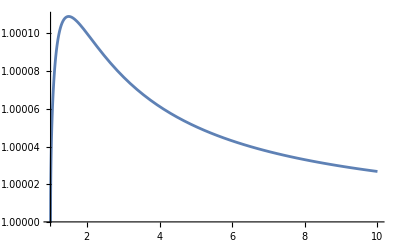

```mathematica
(x^3 E2[x])/((x^3+2 (-2 G M+x) ζ^2) E2[x]-2 ζ √(-x^6+(-2 G M+x) (x^3+(-2 G M+x) ζ^2) E2[x]^2))/.E2[x]->I  x/.G->1/.M->1/.ζ->10^-4//FullSimplify
Plot[%,{x,1,10},PlotRange->All]
```

```mathematica
NxValue=Nx[x]->(Nx[x]/.NxRule//TrigToExp//Expand)/.Exp[Times[a___]K2[x]/x]:>ξ^(a/(2I ζ))/.solveK2/.stationaryN//FullSimplify[#,ζ>0&&E2[x]>0&&G>0]&
```

{Nx[x]→-(ⅈ C[1] √(-x^6+(-2 G M+x) (x^3+(-2 G M+x) ζ^2) E2[x]^2))/(x E2[x]^2),Nx[x]→(ⅈ C[1] √(-x^6+(-2 G M+x) (x^3+(-2 G M+x) ζ^2) E2[x]^2))/(x E2[x]^2)}

```mathematica
Ds2=-NN[x]^2 Dt^2+E2[x]^2/E1[x](Dx+Nx[x] Dt)^2;
gmetric=CoefficientArrays[Ds2,{Dt,Dx},"Symmetric"->True]//Last//Normal;
(gmetric=gmetric/.arealGF/.stationaryN/.Last[NxValue])//MatrixForm
```

(-(x^2 C[1]^2)/E2[x]^2-(C[1]^2 (-x^6+(-2 G M+x) (x^3+(-2 G M+x) ζ^2) E2[x]^2))/(x^4 E2[x]^2) | (ⅈ C[1] √(-x^6+(-2 G M+x) (x^3+(-2 G M+x) ζ^2) E2[x]^2))/x^3
(ⅈ C[1] √(-x^6+(-2 G M+x) (x^3+(-2 G M+x) ζ^2) E2[x]^2))/x^3 | E2[x]^2/x^2)

```mathematica
sChGauge=Solve[0==gmetric[[1,2]]^2//FullSimplify,E2[x]]//FullSimplify[#,x>0]&
MatrixForm/@(gmetric/.sChGauge/.C[1]->1//FullSimplify//ExpandAll)
```

{{E2[x]→-x^3/(√((-2 G M+x) (x^3+(-2 G M+x) ζ^2)))},{E2[x]→x^3/(√((-2 G M+x) (x^3+(-2 G M+x) ζ^2)))}}

{(-1+(2 G M)/x-(4 G^2 M^2 ζ^2)/x^4+(4 G M ζ^2)/x^3-ζ^2/x^2 | 0
0 | x^4/(-2 G M x^3+x^4+4 G^2 M^2 ζ^2-4 G M x ζ^2+x^2 ζ^2)),(-1+(2 G M)/x-(4 G^2 M^2 ζ^2)/x^4+(4 G M ζ^2)/x^3-ζ^2/x^2 | 0
0 | x^4/(-2 G M x^3+x^4+4 G^2 M^2 ζ^2-4 G M x ζ^2+x^2 ζ^2))}

```mathematica
(PGgauge=gmetric/.E2[x]-> x/.C[1]->1)//FullSimplify//ExpandAll;
(PGgauge=PGgauge/.Times[I,a__]:>√(-Times[a]^2)//ExpandAll)//MatrixForm
```

(-1+(2 G M)/x-(4 G^2 M^2 ζ^2)/x^4+(4 G M ζ^2)/x^3-ζ^2/x^2 | √((2 G M)/x-(4 G^2 M^2 ζ^2)/x^4+(4 G M ζ^2)/x^3-ζ^2/x^2)
√((2 G M)/x-(4 G^2 M^2 ζ^2)/x^4+(4 G M ζ^2)/x^3-ζ^2/x^2) | 1)

```mathematica
PGgauge==(-Dt^2+(Dx+√((2G M)/x-ζ^2/x^2((2G M)/x-1)^2)Dt)^2//CoefficientArrays[#,{Dt,Dx},"Symmetric"->True]&//Last//Normal)//FullSimplify
```

True

## Solve the polymerized Hamiltonian Constraint: case 2

```mathematica
Heff2Polymer=Heff2/.polymerRule/.(3 Cos[(2 ζ K2[x])/(√E1[x])] √E1[x] E2[x])/(4 G ζ^2)->(3 (1-2 Sin[(ζ K2[x])/(√E1[x])]^2) √E1[x] E2[x])/(4 G ζ^2)//Expand
```

-E2[x]/(2 G √E1[x])-(3 √E1[x] E2[x] Sin[(ζ K2[x])/(√E1[x])]^2)/(2 G ζ^2)-(E1[x] K1[x] Sin[(2 ζ K2[x])/(√E1[x])])/(2 G ζ)+(E2[x] K2[x] Sin[(2 ζ K2[x])/(√E1[x])])/(2 G ζ)+E1'[x]^2/(16 G √E1[x] E2[x])+(Cos[(2 ζ K2[x])/(√E1[x])] E1'[x]^2)/(16 G √E1[x] E2[x])-(ζ K1[x] Sin[(2 ζ K2[x])/(√E1[x])] E1'[x]^2)/(8 G E2[x]^2)+(ζ K2[x] Sin[(2 ζ K2[x])/(√E1[x])] E1'[x]^2)/(8 G E1[x] E2[x])-(√E1[x] E1'[x] E2'[x])/(4 G E2[x]^2)-(Cos[(2 ζ K2[x])/(√E1[x])] √E1[x] E1'[x] E2'[x])/(4 G E2[x]^2)+(√E1[x] E1''[x])/(4 G E2[x])+(Cos[(2 ζ K2[x])/(√E1[x])] √E1[x] E1''[x])/(4 G E2[x])

```mathematica
mu2Polymer=mu2/.sRule/.polymerRule
```

Cos[(ζ K2[x])/(√E1[x])]^2+(ζ^2 Cos[(ζ K2[x])/(√E1[x])]^2 E1'[x]^2)/(4 E1[x] E2[x]^2)

```mathematica
NxRule=poissonFun[{FF[x](E1[x]-x^2),NN[x]Heff2Polymer+Nx[x] HvGau},canonicalPairs]==0;
NxRule=Solve[NxRule,Nx[x]]//First//FullSimplify;
NxRule=NxRule/.arealGF//Refine[#,x>0]&
```

{Nx[x]→-((4 x^2 ζ^2+4 x^2 E2[x]^2) NN[x] Sin[(2 ζ K2[x])/x])/(8 x ζ E2[x]^2)}

```mathematica
Heff2ArealGF=Heff2Polymer/.arealGF//Refine[#,x>0]&
```

(3 x)/(4 G E2[x])+(3 x Cos[(2 ζ K2[x])/x])/(4 G E2[x])-E2[x]/(2 G x)-(3 x E2[x] Sin[(ζ K2[x])/x]^2)/(2 G ζ^2)+(ζ K2[x] Sin[(2 ζ K2[x])/x])/(2 G E2[x])+(E2[x] K2[x] Sin[(2 ζ K2[x])/x])/(2 G ζ)-(x^2 E2'[x])/(2 G E2[x]^2)-(x^2 Cos[(2 ζ K2[x])/x] E2'[x])/(2 G E2[x]^2)-(x ζ Sin[(2 ζ K2[x])/x] K2'[x])/(2 G E2[x])-(x E2[x] Sin[(2 ζ K2[x])/x] K2'[x])/(2 G ζ)

```mathematica
stationaryN=poissonFun[{FF[x]E2[x],NN[x]Heff2ArealGF},canonicalPairs]//Expand//FullSimplify
stationaryN=DSolve[stationaryN==0,NN[x],x]//First
```

-((ζ^2+E2[x]^2) FF[x] Sin[(2 ζ K2[x])/x] (x NN[x] E2'[x]+E2[x] (-NN[x]+x NN'[x])))/(2 ζ E2[x]^2)

{NN[x]→(x C[1])/E2[x]}

```mathematica
solveK2=-x/E2[x] Heff2ArealGF//Expand//Integrate[#,x]&//Expand
solveK2=(solveK2-M)/. Cos[z_]^2:>1/2 Cos[2z]+1/2//Expand
solveK2=Solve[solveK2==0,Cos[(2ζ K2[x])/x]]//First
```

x/(2 G)+x^3/(4 G ζ^2)-(x^3 Cos[(2 ζ K2[x])/x])/(4 G ζ^2)-(x^3 Cos[(ζ K2[x])/x]^2)/(2 G E2[x]^2)

-M+x/(2 G)+x^3/(4 G ζ^2)-(x^3 Cos[(2 ζ K2[x])/x])/(4 G ζ^2)-x^3/(4 G E2[x]^2)-(x^3 Cos[(2 ζ K2[x])/x])/(4 G E2[x]^2)

{Cos[(2 ζ K2[x])/x]→(-x^3 ζ^2+x^3 E2[x]^2-4 G M ζ^2 E2[x]^2+2 x ζ^2 E2[x]^2)/(x^3 (ζ^2+E2[x]^2))}

```mathematica
NxValue=Nx[x]->(Nx[x]/.NxRule/.Sin[a_]:>-√(1-Cos[a]^2)/.solveK2)/.stationaryN//FullSimplify[#,ζ>0&&E2[x]>0&&x>0]&
```

Nx[x]→(C[1] √((x^3+(-2 G M+x) ζ^2) (x^3+(2 G M-x) E2[x]^2)))/(x E2[x]^2)

```mathematica
mu2PolymerGF=(mu2Polymer/.arealGF//Simplify[#,x>0]&)/. Cos[z_]^2:>1/2 Cos[2z]+1/2/.solveK2//FullSimplify
```

1+((-2 G M+x) ζ^2)/x^3

```mathematica
Ds2=-NN[x]^2 Dt^2+E2[x]^2/(mu2PolymerGF  E1[x])(Dx+Nx[x] Dt)^2;
gmetric=CoefficientArrays[Ds2,{Dt,Dx},"Symmetric"->True]//Last//Normal;
(gmetric=(gmetric/.arealGF/.stationaryN/.NxValue//FullSimplify[#,ζ>0&&E2[x]>0&&x>0]&)/.a_/(√b_):>√(a^2/b//FullSimplify))//MatrixForm
```

(-((-2 G M+x) C[1]^2)/x | (C[1] √((x^3+(-2 G M+x) ζ^2) (x^3+(2 G M-x) E2[x]^2)))/(x^3+(-2 G M+x) ζ^2)
(C[1] √((x^3+(-2 G M+x) ζ^2) (x^3+(2 G M-x) E2[x]^2)))/(x^3+(-2 G M+x) ζ^2) | (x E2[x]^2)/(x^3+(-2 G M+x) ζ^2))

```mathematica
schGauge=Solve[0==gmetric[[1,2]]^2//FullSimplify,E2[x]]//FullSimplify[#,x>0]&
schGauge=(gmetric/.schGauge/.C[1]->1//FullSimplify);
MatrixForm/@sChGauge
```

{{E2[x]→-x^(3/2)/(√(-2 G M+x))},{E2[x]→x^(3/2)/(√(-2 G M+x))}}

{(E2[x]→-x^3/(√((-2 G M+x) (x^3+(-2 G M+x) ζ^2)))),(E2[x]→x^3/(√((-2 G M+x) (x^3+(-2 G M+x) ζ^2))))}

```mathematica
(PGgauge=gmetric/.E2[x]-> x/.C[1]->1)//FullSimplify//ExpandAll;
(PGgauge=(PGgauge//FullSimplify[#,ζ>0&&G>0&&M>0&&x>0]&))//MatrixForm
```

(-1+(2 G M)/x | (√2 G M x)/(√(G M (x^3+(-2 G M+x) ζ^2)))
(√2 G M x)/(√(G M (x^3+(-2 G M+x) ζ^2))) | x^3/(x^3+(-2 G M+x) ζ^2))

```mathematica
({Dt,Dx}.PGgauge.{Dt,Dx}+Dt^2-(1+ζ^2/x^2-(2G M ζ^2)/x^3)^-1(Dx+√((2G M)/x(1+ζ^2/x^2-(2G M ζ^2)/x^3))Dt)^2//FullSimplify[#,x>0&&M>0&&(x^3+(-2 M+x) ζ^2)>0&&G>0]&)/.a_/(√b_):>√(a^2/b//FullSimplify)
```

0

```mathematica
transM={{a,b},{0,1}};
```

```mathematica
transedMetric=Transpose[transM].PGgauge.transM//FullSimplify;
equs=transedMetric-schGauge[[1]]//Flatten;
solb=Solve[equs[[-1]]==0,b]//FullSimplify
sola=Solve[equs[[1]]==0,a]//FullSimplify
equs[[2]]/.sola/.solb//FullSimplify
```

{{b→-(√2 G M x^2)/((2 G M-x) √(G M (x^3+(-2 G M+x) ζ^2)))},{b→-(√2 G M x^2)/((2 G M-x) √(G M (x^3+(-2 G M+x) ζ^2)))}}

{{a→-1},{a→1}}

{{0,0},{0,0}}

```mathematica
transMP={{a,1},{Derivative[1][R][T],0}};
(metricHom=(Transpose[transMP].PGgauge.transMP//FullSimplify)/.x->R[T])//MatrixForm;
solaa=Solve[metricHom[[1,2]]==0,a]//FullSimplify//First;
metricHom[[1,1]]/.solaa//FullSimplify;
%/.R'[T]->-R[T]^3/(ζ^2+3 R[T]^2 Sin[T]^2)((2 ζ √(2 G M-R[T]) √(1+(ζ^2 (-2 G M+R[T]))/R[T]^3))/R[T]^(3/2))//FullSimplify
%%/.R'[T]->-(2 R[T]^3 Sin[T]Cos[T])/(ζ^2+3 R[T]^2 Sin[T]^2)//FullSimplify
%/.Sin[2T]^2->-(4 ζ^2 (2 G M-R[T]) (2 G M ζ^2-R[T] (ζ^2+R[T]^2)))/R[T]^6//FullSimplify
```

-(4 ζ^2 R[T]^4)/((ζ^2+3 R[T]^2 Sin[T]^2)^2)

(R[T]^10 Sin[2 T]^2)/((-2 G M+R[T]) (-2 G M ζ^2+ζ^2 R[T]+R[T]^3) (ζ^2+3 R[T]^2 Sin[T]^2)^2)

-(4 ζ^2 R[T]^4)/((ζ^2+3 R[T]^2 Sin[T]^2)^2)

## Homogeneous solution of the second spacetime

```mathematica
Heff2Hom=Heff2Polymer/.Derivative[_][_][x]:>0
```

-E2[x]/(2 G √E1[x])-(3 √E1[x] E2[x] Sin[(ζ K2[x])/(√E1[x])]^2)/(2 G ζ^2)-(E1[x] K1[x] Sin[(2 ζ K2[x])/(√E1[x])])/(2 G ζ)+(E2[x] K2[x] Sin[(2 ζ K2[x])/(√E1[x])])/(2 G ζ)

```mathematica
Meff2Hom=Meff2/.sRule/.polymerRule/.Derivative[_][_][x]:>0
```

(√E1[x])/(2 G)+(E1[x]^(3/2) Sin[(ζ K2[x])/(√E1[x])]^2)/(2 G ζ^2)

```mathematica
homGauge=E1[x]->t^2
dotE1=poissonFun[{E1[x],Heff2Hom NN[x]},canonicalPairs]//FullSimplify
dotE1=dotE1/.homGauge//Simplify[#,t>0]&;
meffGauge=Meff2Hom-M/.homGauge//Simplify[#,t>0]&;
variable=Cases[meffGauge,_Sin,Infinity]//First;
meffGauge=Solve[meffGauge==0,variable]
dotE1=dotE1/.Sin[x_]:>2Sin[x/2] √(1-Sin[x/2]^2)/.meffGauge;
equs=dotE1==2 t//Thread
solNN=Solve[#,NN[x]]&/@equs//FullSimplify//Flatten[#,1]&
NNK2Rule=Flatten/@({meffGauge,solNN}//Transpose)
```

E1[x]→t^2

(E1[x] NN[x] Sin[(2 ζ K2[x])/(√E1[x])])/ζ

{{Sin[(ζ K2[x])/t]→-(√(2 G M-t) ζ)/t^(3/2)},{Sin[(ζ K2[x])/t]→(√(2 G M-t) ζ)/t^(3/2)}}

{-2 √(2 G M-t) √t √(1-((2 G M-t) ζ^2)/t^3) NN[x]==2 t,2 √(2 G M-t) √t √(1-((2 G M-t) ζ^2)/t^3) NN[x]==2 t}

{{NN[x]→-(√t)/(√(2 G M-t) √(1+((-2 G M+t) ζ^2)/t^3))},{NN[x]→(√t)/(√(2 G M-t) √(1+((-2 G M+t) ζ^2)/t^3))}}

{{Sin[(ζ K2[x])/t]→-(√(2 G M-t) ζ)/t^(3/2),NN[x]→-(√t)/(√(2 G M-t) √(1+((-2 G M+t) ζ^2)/t^3))},{Sin[(ζ K2[x])/t]→(√(2 G M-t) ζ)/t^(3/2),NN[x]→(√t)/(√(2 G M-t) √(1+((-2 G M+t) ζ^2)/t^3))}}

```mathematica
dotE2=poissonFun[{E2[x],Heff2Hom NN[x]},canonicalPairs]//FullSimplify;
dotE2=dotE2/.homGauge//Simplify[#,t>0]&
constraint=Heff2Hom/.homGauge//Simplify[#,t>0]&;
constraint=Solve[constraint==0,K1[x]]//First
dotE2=dotE2/.constraint/.NNK2Rule//FullSimplify
dotE2=dotE2/.Sin[2x_]:>2Sin[x] √(1-Sin[x]^2)/.Cot[x_]:>(1-2 Sin[x/2]^2)/(2Sin[x/2] √(1-Sin[x/2]^2))/.Csc[x_]:>HoldForm[1/Sin[x]];
dotE2=MapThread[#1/.#2&,{dotE2,meffGauge}]//ReleaseHold//FullSimplify//DeleteDuplicates
Integrate[#/E2[x],t]&/@dotE2
```

NN[x] (t Cos[(2 ζ K2[x])/t] K1[x]+E2[x] (-(Cos[(2 ζ K2[x])/t] K2[x])/t+Sin[(2 ζ K2[x])/t]/ζ))

{K1[x]→-(E2[x] (ζ^2 Csc[(2 ζ K2[x])/t]-t ζ K2[x]+3 t^2 Csc[(2 ζ K2[x])/t] Sin[(ζ K2[x])/t]^2))/(t^3 ζ)}

{(E2[x] (2 (3 G M-t) ζ^2 Cot[(2 ζ K2[x])/t]-t^3 Sin[(2 ζ K2[x])/t]))/(√(2 G M-t) t^(5/2) ζ √(1+((-2 G M+t) ζ^2)/t^3)),(E2[x] (2 (-3 G M+t) ζ^2 Cot[(2 ζ K2[x])/t]+t^3 Sin[(2 ζ K2[x])/t]))/(√(2 G M-t) t^(5/2) ζ √(1+((-2 G M+t) ζ^2)/t^3))}

{((t^3 (-G M+t)+2 G M (-2 G M+t) ζ^2) E2[x])/(t (-2 G M+t) (t^3+(-2 G M+t) ζ^2))}

{-Log[t]+1/2 Log[-2 G M+t]+1/2 Log[t^3-2 G M ζ^2+t ζ^2]}

### second Gauge

```mathematica
homGauge2=K2[x]->(√E1[x] t)/ζ;
dotE1=poissonFun[{E1[x],NN[x]Heff2Hom},canonicalPairs]/.homGauge2
meffGauge2=Meff2Hom-M/.homGauge2/.E1[x]->R[t]^2//Simplify[#,R[t]>0]&;
RofT=(Solve[meffGauge2==0,R[t]]//First//FullSimplify[#,Sin[t]>0]&)
RofT/.-9 G M ζ^2 Sin[t]+√3 √(ζ^6+27 G^2 M^2 ζ^4 Sin[t]^2)->1/3 β[t]^3//FullSimplify[#,β[t]>0]&
dotR=poissonFun[{√E1[x],NN[x]Heff2Hom},canonicalPairs]/.homGauge2/.E1[x]->R[t]^2//Simplify[#,R[t]>0]&
```

(E1[x] NN[x] Sin[2 t])/ζ

{R[t]→(Csc[t] (-3^(2/3) ζ^2+3^(1/3) (9 G M ζ^2 Sin[t]+√3 √(ζ^6+27 G^2 M^2 ζ^4 Sin[t]^2))^(2/3)))/(3 (9 G M ζ^2 Sin[t]+√3 √(ζ^6+27 G^2 M^2 ζ^4 Sin[t]^2))^(1/3))}

{R[t]→(Csc[t] (-3^(2/3) ζ^2+3^(1/3) (9 G M ζ^2 Sin[t]+√3 √(ζ^6+27 G^2 M^2 ζ^4 Sin[t]^2))^(2/3)))/(3 (9 G M ζ^2 Sin[t]+√3 √(ζ^6+27 G^2 M^2 ζ^4 Sin[t]^2))^(1/3))}

(Cos[t] NN[x] R[t] Sin[t])/ζ

```mathematica
dotM=(D[meffGauge2,t])//Expand
dolDotR=Solve[dotM==0,R'[t]]//First
Solve[R'[t]==dotR/.dolDotR,NN[x]]
```

(Cos[t] R[t]^3 Sin[t])/(G ζ^2)+R'[t]/(2 G)+(3 R[t]^2 Sin[t]^2 R'[t])/(2 G ζ^2)

{R'[t]→-(2 Cos[t] R[t]^3 Sin[t])/(ζ^2+3 R[t]^2 Sin[t]^2)}

{{NN[x]→-(2 ζ R[t]^2)/(ζ^2+3 R[t]^2 Sin[t]^2)}}

```mathematica
dotE2=poissonFun[{E2[x],Heff2Hom NN[x]},canonicalPairs]//FullSimplify;
K1sol=Solve[Heff2Hom==0,K1[x]]//First;
dotE2=dotE2/.K1sol/.homGauge2/.E1[x]->R[t]^2//Simplify[#,R[t]>0]&//FullSimplify;
NNinDotR=Solve[D[R[t],t]==dotR,NN[x]]//First
dotE2=dotE2/.NNinDotR//FullSimplify
sint=Solve[meffGauge2==0,Sin[t]]//Last
dotE21=dotE2/.t->ArcSin[Sin[t]/.sint]/.{R[_]:>R[t],R'[_]->R'[t]}//FullSimplify
dotE22=dotE2/.t->Pi-ArcSin[Sin[t]/.sint]/.{R[_]:>R[t],R'[_]->R'[t]}//FullSimplify
dotE21-dotE21//FullSimplify
```

{NN[x]→(ζ Csc[t] Sec[t] R'[t])/R[t]}

-(E2[x] Sec[t] (2 ζ^2 Cot[2 t] Csc[t]+(-2+Cos[2 t]) R[t]^2 Sec[t]) R'[t])/(2 R[t]^3)

{Sin[t]→(ζ √(2 G M-R[t]))/R[t]^(3/2)}

(E2[x] (4 G^2 M^2 ζ^2-2 G M ζ^2 R[t]+G M R[t]^3-R[t]^4) R'[t])/((2 G M-R[t]) R[t] (-2 G M ζ^2+ζ^2 R[t]+R[t]^3))

(E2[x] (-4 G^2 M^2 ζ^2+2 G M ζ^2 R[t]-G M R[t]^3+R[t]^4) R'[t])/((2 G M-R[t]) R[t] (2 G M ζ^2-R[t] (ζ^2+R[t]^2)))

0

```mathematica
(dotE21/(E2[x] R'[t])/.R[t]->y//Integrate[#,y]&//Exp)/.y->R[t]
```

(√(-2 G M+R[t]) √(-2 G M ζ^2+ζ^2 R[t]+R[t]^3))/R[t]

## Spacetime Properties: the first model

```mathematica
f1=(2M)/x-ζ^2/x^2(2 M/x-1)^2
```

(2 M)/x-((-1+(2 M)/x)^2 ζ^2)/x^2

```mathematica
(Solve[1-f1==0,x]//FullSimplify[#,α>0]&)/.(-9 M ζ^2+√3 √(27 M^2 ζ^4+ζ^6))->1/3( β )^3//FullSimplify[#,β>0&&ζ>0]&//Expand
```

{{x→2 M},{x→-β/3+ζ^2/β},{x→-1/3 (-1)^(2/3) β-((-1)^(1/3) ζ^2)/β},{x→1/3 (-1)^(1/3) β+((-1)^(2/3) ζ^2)/β}}

```mathematica
metric1={{-1-f1,0,0,0},{0,(1-f1)^(-1),0,0},{0,0,x^2,0},{0,0,0,x^2 Sin[θ]^2}};
coor={t,x,θ,ϕ};
Racci1=racciCurFromMetric[coor,metric1]//FullSimplify;
G1=Racci1-1/2 metric1 Tr[Racci1.Inverse[metric1]]//FullSimplify;
-G1[[1,1]]/metric1[[1,1]]//FullSimplify
%/.M->0
```

((-6 M+x) (-2 M+x) ζ^2)/x^6

ζ^2/x^4

## Spacetime properties: the second property

```mathematica
g00=-(4 ζ^2 R[t]^4)/((ζ^2+3 R[t]^2 Sin[t]^2)^2);
g11=-1+(2 M)/R[t];
```

```mathematica
Rfun=R->Function[t,(Csc[t] (3^(2/3) ζ^2-3^(1/3) (-9 M ζ^2 Sin[t]+√3 √(ζ^6+27 M^2 ζ^4 Sin[t]^2))^(2/3)))/(3 (-9 M ζ^2 Sin[t]+√3 √(ζ^6+27 M^2 ζ^4 Sin[t]^2))^(1/3))];
```

```mathematica
g2={{g00,0,0,0},{0,g11,0,0},{0,0,R[t]^2,0},{0,0,0,R[t]^2 Sin[θ]^2}};
coor2={t,x,θ,ϕ}
racciScalar=racciCurFromMetric[coor,g2].Inverse[g2]//Tr//Simplify;
racciScalar=racciScalar/.Rfun/.t->Pi/2;
```

{t,x,θ,ϕ}

```mathematica
g2Sch={{-(1-(2M)/x),0,0,0},{0,(1+ζ^2/x^2(1-(2M)/x))^-1(1-(2M)/x)^-1,0,0},{0,0,x^2,0},{0,0,0,x^2 Sin[θ]^2}};
coor={t,x,θ,ϕ};
racciScalarSchFun=racciCurFromMetric[coor,g2Sch].Inverse[g2Sch]//Tr//Expand//FullSimplify;
racciScalarSch=(racciScalarSchFun/.Solve[(1+ζ^2/x^2(1-(2M)/x))==0,x]//First//FullSimplify)
```

(162 (9 M ζ^3+√3 ζ √(27 M^2 ζ^4+ζ^6))^2 (9 M^2-(2 ζ^2)/3+ζ^4/(3^(2/3) (9 M ζ^2+√3 √(27 M^2 ζ^4+ζ^6))^(2/3))+((9 M ζ^2+√3 √(27 M^2 ζ^4+ζ^6))^(2/3))/(3 3^(1/3))+(7 M (3^(1/3) ζ^2-(9 M ζ^2+√3 √(27 M^2 ζ^4+ζ^6))^(2/3)))/(3 (3 M ζ^2+√(9 M^2 ζ^4+ζ^6/3))^(1/3))))/((-3^(1/3) ζ^2+(9 M ζ^2+√3 √(27 M^2 ζ^4+ζ^6))^(2/3))^6)

```mathematica
(racciScalar-racciScalarSch)/.{M->SetPrecision[RandomReal[],200],ζ->1}
```

0.

```mathematica
Series[racciScalarSch,{M,Infinity,1}]//Simplify[#,M>0&&ζ>0]&
{racciScalarSch,Normal[%]}/.{M->RandomReal[{1000,10000}],ζ->1.}
```

9/(2 ζ^2)+(2^(1/3) (1/M)^(2/3))/ζ^(4/3)+O[1/M]^(4/3)

{4.50674,4.50673}

```mathematica
racciScalarSchFun/.x->2M
```

-ζ^2/(32 M^4)

```mathematica
invg2Sch=Inverse[g2Sch]//Simplify;
```

```mathematica
riemann=riemannTensorFromMetric[coor,g2Sch];
```

```mathematica
Kretschmann=Sum[riemann[[a,b,c,d]]riemann[[ap,bp,cp,dp]]invg2Sch[[a,ap]]invg2Sch[[b,bp]]invg2Sch[[c,cp]]g2Sch[[d,dp]],{a,1,4},{b,1,4},{c,1,4},{d,1,4},{ap,1,4},{bp,1,4},{cp,1,4},{dp,1,4}]//Simplify
```

(4 (201 M^4 ζ^4+3 x^4 ζ^4-8 M x^3 ζ^2 (x^2+4 ζ^2)-2 M^3 (42 x^3 ζ^2+137 x ζ^4)+M^2 (12 x^6+56 x^4 ζ^2+139 x^2 ζ^4)))/x^12

```mathematica
Kretschmann/.Solve[(1+ζ^2/x^2(1-(2M)/x))==0,x]//First//Simplify//Series[#,{M,Infinity,1}]&//Simplify[#,M>0&&ζ>0]&
```

81/(4 ζ^4)+(9 2^(1/3) (1/M)^(2/3))/ζ^(10/3)+O[1/M]^(4/3)

```mathematica
Plot[Kretschmann/.{ζ->1,M->1000},{x,0.1,1}]
```

-Graphics-

## Check the spacetime

```mathematica
g2Sch={{-(1-(2M)/x),0,0,0},{0,(1+ζ^2/x^2(1-(2M)/x))^-1(1-(2M)/x)^-1,0,0},{0,0,x^2,0},{0,0,0,x^2 Sin[θ]^2}};
g2Schp={{-(1-(2M)/x),0,0,0},{0,(1-(2ζ M)/x)^-1(1-(2M)/x)^-1,0,0},{0,0,x^2,0},{0,0,0,x^2 Sin[θ]^2}};
coor={t,x,θ,ϕ};
```

```mathematica
R2=racciCurFromMetric[coor,g2Sch].Inverse[g2Sch]//Tr//Expand//FullSimplify
R2p=racciCurFromMetric[coor,g2Schp].Inverse[g2Schp]//Tr//Expand//Simplify
```

(2 (9 M^2-7 M x+x^2) ζ^2)/x^6

(6 M^2 ζ)/x^4

```mathematica
(R2/.Solve[(1+ζ^2/x^2(1-(2M)/x))==0,x]//First//FullSimplify)
Limit[%,M->Infinity]//FullSimplify[#,M>0&ζ>0]&
Series[%%,{M,Infinity,1}]//FullSimplify[#,M>0&ζ>0]&
```

(162 (9 M ζ^3+√3 ζ √(27 M^2 ζ^4+ζ^6))^2 (9 M^2-(2 ζ^2)/3+ζ^4/(3^(2/3) (9 M ζ^2+√3 √(27 M^2 ζ^4+ζ^6))^(2/3))+((9 M ζ^2+√3 √(27 M^2 ζ^4+ζ^6))^(2/3))/(3 3^(1/3))+(7 M (3^(1/3) ζ^2-(9 M ζ^2+√3 √(27 M^2 ζ^4+ζ^6))^(2/3)))/(3 (3 M ζ^2+√(9 M^2 ζ^4+ζ^6/3))^(1/3))))/((-3^(1/3) ζ^2+(9 M ζ^2+√3 √(27 M^2 ζ^4+ζ^6))^(2/3))^6)

9/(2 ζ^2)

9/(2 ζ^2)+(2^(1/3) (1/M)^(2/3))/Abs[ζ]^(4/3)+O[1/M]^(4/3)

```mathematica
Ds2=-Dt^2 NN[x]^2+(E2[x]^2 (Dx+Dt Nx[x])^2)/(μ E1[x])+ E1[x](Dθ^2+Sin[θ]^2 Dϕ^2)
CoefficientArrays[Ds2,{Dt,Dx,Dθ,Dϕ},"Symmetric"->True]//Last//Normal//Inverse//FullSimplify//MatrixForm
```

-Dt^2 NN[x]^2+(E2[x]^2 (Dx+Dt Nx[x])^2)/(μ E1[x])+E1[x] (Dθ^2+Dϕ^2 Sin[θ]^2)

(-1/NN[x]^2 | Nx[x]/NN[x]^2 | 0 | 0
Nx[x]/NN[x]^2 | (μ E1[x])/E2[x]^2-Nx[x]^2/NN[x]^2 | 0 | 0
0 | 0 | 1/E1[x] | 0
0 | 0 | 0 | Csc[θ]^2/E1[x])

## Coordinate cover the wormhole in the third spacetime

```mathematica
Heff3Polymer=Heff3/.λ->Function[x,ζ^2/x]/.ψ->Function[x,0]
```

(Cos[(ζ^2 (1+K2[x]^2-E1'[x]^2/(4 E2[x]^2)))/E1[x]] E2[x])/(G √E1[x])-(Cos[(ζ^2 (1+K2[x]^2-E1'[x]^2/(4 E2[x]^2)))/E1[x]] √E1[x] K1[x] K2[x])/G+(Cos[(ζ^2 (1+K2[x]^2-E1'[x]^2/(4 E2[x]^2)))/E1[x]] E2[x] K2[x]^2)/(G √E1[x])-(3 √E1[x] E2[x] Sin[(ζ^2 (1+K2[x]^2-E1'[x]^2/(4 E2[x]^2)))/E1[x]])/(2 G ζ^2)-(Cos[(ζ^2 (1+K2[x]^2-E1'[x]^2/(4 E2[x]^2)))/E1[x]] E1'[x]^2)/(4 G √E1[x] E2[x])-(Cos[(ζ^2 (1+K2[x]^2-E1'[x]^2/(4 E2[x]^2)))/E1[x]] √E1[x] E1'[x] E2'[x])/(2 G E2[x]^2)+(Cos[(ζ^2 (1+K2[x]^2-E1'[x]^2/(4 E2[x]^2)))/E1[x]] √E1[x] E1''[x])/(2 G E2[x])

```mathematica
Meff3Polymer=Meff3sRule/.λ->Function[x,ζ^2/x]/.ψ->Function[x,0]
```

(E1[x]^(3/2) Sin[(ζ^2 (1+K2[x]^2-E1'[x]^2/(4 E2[x]^2)))/E1[x]])/(2 G ζ^2)

```mathematica
wormholeGauge=E1->Function[x,((2G M ζ^2)/Sin[x])^(2/3)];
wormholeGauge2=DSolve[0==HvGau/.wormholeGauge,K1,x]//First;
wormholeGauge={wormholeGauge,wormholeGauge2}//Flatten//FullSimplify;
wormholeGauge3=K2->Function[x,0];
wormholeGauge4=DSolve[M==Meff3Polymer/.wormholeGauge/.wormholeGauge3,E2,x]/.C[1]->0//FullSimplify[#,x>0&&x<Pi/2&&G>0&&M>0&&ζ>0]&//First;
wormholeGauge={wormholeGauge,wormholeGauge3,wormholeGauge4}//Flatten
```

{E1→Function[x,((2 G M ζ^2)/Sin[x])^(2/3)],K1→Function[{x},-(3 (G M ζ^2 Csc[x])^(1/3) E2[x] Sin[x] Tan[x] K2'[x])/(2^(2/3) G M ζ^2)],K2→Function[x,0],E2→Function[{x},-(2^(5/6) √G √M ζ^2 Cos[x] Csc[x]^(3/2))/(3 (G M ζ^2 Csc[x])^(1/6) √(-2 x+(2^(1/3) (G M ζ^2 Csc[x])^(1/3) Sin[x])/(G M)))]}

```mathematica
mu3Wormhole=1-((2 G ζ^2 M)/E1[x]^(3/2))^2/.wormholeGauge//FullSimplify
```

Cos[x]^2

```mathematica
gxx=E2[x]^2/(E1[x]mu3Wormhole)/.wormholeGauge//FullSimplify[#,x>0&&x<Pi/2&&G>0&&M>0&&ζ>0]&//DeleteDuplicates
gxx==(((2 G M ζ^2)/Sin[x])^(2/3))/(9(1-((2 G M)/(ζ Sin[x]))^(2/3)x)Sin[x]^2)//FullSimplify[#,x>0&&x<Pi/2&&G>0&&M>0&&ζ>0]&
```

(2 G M ζ^2 Csc[x]^2)/(9 (-2 G M x+2^(1/3) (G M ζ^2 Sin[x]^2)^(1/3)))

True

```mathematica
dotE1Eff3=poissonFun[{E1[x],Heff3Polymer NN[x]+HvGau Nx[x]},canonicalPairs]/.wormholeGauge//Simplify
Solve[dotE1Eff3==0,Nx[x]]
```

-2/3 2^(2/3) Cot[x] (G M ζ^2 Csc[x])^(2/3) Nx[x]

{{Nx[x]→0}}

```mathematica
dotK2Eff3=poissonFun[{K2[x],Heff3Polymer NN[x]},canonicalPairs]//.wormholeGauge//Simplify
dotK2Eff3/.NN->Function[x,√(1-((2 G M)/(ζ Sin[x]))^(2/3)x)]//FullSimplify[#,x>0&&x<Pi/2&&G>0&&M>0&&ζ>0]&
```

(G M (-3+2 x Cot[x]) NN[x]-3 (-2 G M x+2^(1/3) (G M ζ^2 Csc[x])^(1/3) Sin[x]) NN'[x])/(2^(2/3) (G M ζ^2 Csc[x])^(2/3))

dotK2Eff3/.NN→Function[x,√(1-((2 G M)/(ζ Sin[x]))^(2/3) x)] FullSimplify[#1,x>0&&x<π/2&&G>0&&M>0&&ζ>0]&

## Try to relax assumption on derivative of K2

```mathematica
sRule={s1,s2,s3,s4,s5,s6,s7,s8,s9}->Flatten[{allScalars,K2'[x]/E2[x],(-K2'[x] E2'[x]+E2[x] K2''[x])/E2[x]^3}]//Thread
```

{s1→E1[x],s2→K2[x],s3→K1[x]/E2[x],s4→E1'[x]/E2[x],s5→E1'[x]/K1[x],s6→(-E1'[x] E2'[x]+E2[x] E1''[x])/E2[x]^3,s7→(-E1'[x] E2'[x]+E2[x] E1''[x])/(E2[x]^2 K1[x]),s8→K2'[x]/E2[x],s9→(-E2'[x] K2'[x]+E2[x] K2''[x])/E2[x]^3}

```mathematica
solE13=Solve[D[s6/.sRule,x]==s6p,Derivative[3][E1][x]]//First
solK11=Solve[D[s3/.sRule,x]==s3p,K1'[x]]//First
solK22=Solve[D[s8/.sRule,x]==s8p,K2''[x]]//First
```

{E1^(3)[x]→(s6p E2[x]^4-3 E1'[x] E2'[x]^2+3 E2[x] E2'[x] E1''[x]+E2[x] E1'[x] E2''[x])/E2[x]^2}

{K1'[x]→(s3p E2[x]^2+K1[x] E2'[x])/E2[x]}

{K2''[x]→(s8p E2[x]^2+E2'[x] K2'[x])/E2[x]}

```mathematica
Ffun=F[s1,s2,s3,s4,s6,s8]/.sRule
```

F[E1[x],K2[x],K1[x]/E2[x],E1'[x]/E2[x],(-E1'[x] E2'[x]+E2[x] E1''[x])/E2[x]^3,K2'[x]/E2[x]]

```mathematica
(*If s9 is contained. The poisson bracker will be propotional to -N2'[x] N1''[x]+N1'[x] N2''[x]*)
```

```mathematica
eqs=poissonFun[{N1[x]E2[x]Ffun,N2[x]E2[x]Ffun},canonicalPairs]//Expand;
eqs=(eqs/.Times[a___,Derivative[n_][f_][x]/;MemberQ[{N1,N2},f]&&n≥2]:>(-1)^(n-1)D[Times[a],{x,n-1}]D[f[x],x]//Expand);
eqs=-1/(N2[x] N1'[x]-N1[x] N2'[x])eqs//FullSimplify;
eqs=(eqs-(μ[x]E1[x])/E2[x]^2 HvGau/.solE13/.solK11/.solK22);
eqs=eqs/.E1''[x]->(s6 E2[x]^3+E1'[x] E2'[x])/E2[x]/.E1'[x]->s4 E2[x]/.K2'[x]->s8 E2[x]/.K1[x]->s3 E2[x]/.E1[x]->s1/.K2[x]->s2//FullSimplify;
{eqs,eqs1}=CoefficientList[eqs, s3p]//FullSimplify;
{eqs,eqs2}=CoefficientList[eqs,s8]//FullSimplify;
{eqs,eqs3}=CoefficientList[eqs,s6p]//FullSimplify;
{eqs,eqs4}=CoefficientList[eqs,s8p]//FullSimplify
```

{(s1 s3 s4 μ[x])/(2 G)+G F^(0,0,0,0,0,1)[s1,s2,s3,s4,s6,s8] (F[s1,s2,s3,s4,s6,s8]-s6 F^(0,0,0,0,1,0)[s1,s2,s3,s4,s6,s8])-G (2 F^(0,0,1,0,0,0)[s1,s2,s3,s4,s6,s8] (F^(0,0,0,1,0,0)[s1,s2,s3,s4,s6,s8]-s6 F^(0,0,0,1,1,0)[s1,s2,s3,s4,s6,s8]-s4 F^(1,0,0,0,1,0)[s1,s2,s3,s4,s6,s8])+F^(0,0,0,0,0,1)[s1,s2,s3,s4,s6,s8] (s4 F^(0,0,0,1,0,0)[s1,s2,s3,s4,s6,s8]+s3 F^(0,0,1,0,0,0)[s1,s2,s3,s4,s6,s8]-s4 (s6 F^(0,0,0,1,1,0)[s1,s2,s3,s4,s6,s8]+s4 F^(1,0,0,0,1,0)[s1,s2,s3,s4,s6,s8]))+F^(0,0,0,0,1,0)[s1,s2,s3,s4,s6,s8] (s4 s6 F^(0,0,0,1,0,1)[s1,s2,s3,s4,s6,s8]+2 s6 F^(0,0,1,1,0,0)[s1,s2,s3,s4,s6,s8]+s4 (-F^(0,1,0,0,0,0)[s1,s2,s3,s4,s6,s8]+s4 F^(1,0,0,0,0,1)[s1,s2,s3,s4,s6,s8]+2 F^(1,0,1,0,0,0)[s1,s2,s3,s4,s6,s8]))),1/E2[x]G (-s4 F^(0,0,0,0,0,2)[s1,s2,s3,s4,s6,s8] F^(0,0,0,0,1,0)[s1,s2,s3,s4,s6,s8]+F^(0,0,0,0,1,1)[s1,s2,s3,s4,s6,s8] (s4 F^(0,0,0,0,0,1)[s1,s2,s3,s4,s6,s8]+2 F^(0,0,1,0,0,0)[s1,s2,s3,s4,s6,s8])-2 F^(0,0,0,0,1,0)[s1,s2,s3,s4,s6,s8] F^(0,0,1,0,0,1)[s1,s2,s3,s4,s6,s8])}

```mathematica
eqs4p=eqs4/G E2[x]/.F->Function[{s1,s2,s3,s4,s6,s8},F[a s3+ s6+b s8]]//Expand
eqs3p=eqs3/G E2[x]/.F->Function[{s1,s2,s3,s4,s6,s8},F[a s3+ s6+b s8]]//Expand
eqs1p=eqs1/G E2[x]/.F->Function[{s1,s2,s3,s4,s6,s8},F[a s3+ s6+b s8]]//Expand
```

0

0

0

```mathematica
solF=F->Function[{s1,s2,s3,s4,s6,s8},F[s1,s2,s4,a[s1,s2,s4] s3+s6+b[s1,s2,s4] s8]];
```

```mathematica
solmu=Solve[0==eqs2/.solF,μ[x]]//First;
solmu=μ->Function[{s1,s2,s3,s4,s6,s8},Evaluate[μ[x]/.solmu]]
```

μ→Function[{s1,s2,s3,s4,s6,s8},-1/s1 G^2 (b[s1,s2,s4]^2 (F^(0,0,0,1)[s1,s2,s4,s6+s3 a[s1,s2,s4]+s8 b[s1,s2,s4]])^2+2 a^(0,1,0)[s1,s2,s4] (F^(0,0,0,1)[s1,s2,s4,s6+s3 a[s1,s2,s4]+s8 b[s1,s2,s4]])^2+s4 b^(0,1,0)[s1,s2,s4] (F^(0,0,0,1)[s1,s2,s4,s6+s3 a[s1,s2,s4]+s8 b[s1,s2,s4]])^2)]

```mathematica
muFun=μ[s1,s2,s3,s4,s6,s8]/.sRule;
eqsmu=poissonFun[{λ1[x] muFun/E2[x]^2 E1[x],N2[x]E2[x]Ffun},canonicalPairs]//Expand;
eqsmu=eqsmu/.Times[Derivative[n_][λ1][x],b__]:>(-1)^n λ1[x]D[Times[b],{x,n}]//Expand;
eqsmu1=poissonFun[{λ1[x] muFun/E2[x]^2 E1[x],N2[x]E2[x]α[x]Ffun},canonicalPairs]//Expand;
eqsmu1=eqsmu1/.Times[Derivative[n_][λ1][x],b__]:>(-1)^n λ1[x]D[Times[b],{x,n}]//Expand;
eqsmu=α[x]eqsmu-eqsmu1/.λ1[x]->1//Expand//FullSimplify;
eqsmu1=(Coefficient[eqsmu,α''[x]]//FullSimplify)/.solE13/.solK11/.solK22/.E1''[x]->(s6 E2[x]^3+E1'[x] E2'[x])/E2[x]/.E1'[x]->s4 E2[x]/.K2'[x]->s8 E2[x]/.K1[x]->s3 E2[x]/.E1[x]->s1/.K2[x]->s2//FullSimplify
eqsmu1/.solF/.solmu//Expand
```

1/E2[x]^4 G s1 N2[x] (-s4 μ^(0,0,0,0,0,1)[s1,s2,s3,s4,s6,s8] F^(0,0,0,0,1,0)[s1,s2,s3,s4,s6,s8]+μ^(0,0,0,0,1,0)[s1,s2,s3,s4,s6,s8] (s4 F^(0,0,0,0,0,1)[s1,s2,s3,s4,s6,s8]+2 F^(0,0,1,0,0,0)[s1,s2,s3,s4,s6,s8])-2 F^(0,0,0,0,1,0)[s1,s2,s3,s4,s6,s8] μ^(0,0,1,0,0,0)[s1,s2,s3,s4,s6,s8])

0

```mathematica
eqsmu2=(Coefficient[eqsmu,α'[x]]//FullSimplify)/.solE13/.solK11/.solK22/.E1''[x]->(s6 E2[x]^3+E1'[x] E2'[x])/E2[x]/.E1'[x]->s4 E2[x]/.K2'[x]->s8 E2[x]/.K1[x]->s3 E2[x]/.E1[x]->s1/.K2[x]->s2/.solF/.solmu//Expand//FullSimplify;
eqsmu2=eqsmu2/(-1/E2[x]^3 G^3 N2[x] Derivative[0,0,0,1][F][s1,s2,s4,s6+s3 a[s1,s2,s4]+s8 b[s1,s2,s4]])//FullSimplify//Expand;
{eqsmu2,eqsmu2p}=CoefficientList[eqsmu2,s8];
eqsmu2p//FullSimplify
```

4 (b[s1,s2,s4]^2+s4 b[s1,s2,s4] b^(0,0,1)[s1,s2,s4]+2 (a[s1,s2,s4] b^(0,0,1)[s1,s2,s4]+a^(0,1,0)[s1,s2,s4])) (b[s1,s2,s4]^2+2 a^(0,1,0)[s1,s2,s4]+s4 b^(0,1,0)[s1,s2,s4]) F^(0,0,0,1)[s1,s2,s4,s6+s3 a[s1,s2,s4]+s8 b[s1,s2,s4]] F^(0,0,0,2)[s1,s2,s4,s6+s3 a[s1,s2,s4]+s8 b[s1,s2,s4]]

```mathematica
solFp=F->Function[{s1,s2,s4,z},A[s1,s2,s4]+B[s1,s2,s4]z]
```

F→Function[{s1,s2,s4,z},A[s1,s2,s4]+B[s1,s2,s4] z]

```mathematica
eqsp=eqs/.solF/.solFp//Expand;
{eqsp,eqsp3}=CoefficientList[eqsp,s3]//FullSimplify;
{eqsp,eqsp8}=CoefficientList[eqsp,s8]//FullSimplify;
{eqsp,eqsp6}=CoefficientList[eqsp,s6]//FullSimplify;
```

```mathematica
eqsp8p=eqsp8/G /.a->Function[{s1,s2,s4},F3[s1,s2,s4]/B[s1,s2,s4]]/.b->Function[{s1,s2,s4},F8[s1,s2,s4]/B[s1,s2,s4]]/.B->Function[{s1,s2,s4},F6[s1,s2,s4]]//FullSimplify
eqsp6p=eqsp6/(G F6[s1,s2,s4]) /.a->Function[{s1,s2,s4},F3[s1,s2,s4]/B[s1,s2,s4]]/.b->Function[{s1,s2,s4},F8[s1,s2,s4]/B[s1,s2,s4]]/.B->Function[{s1,s2,s4},F6[s1,s2,s4]]//FullSimplify
eqsp3p=eqsp3/.μ[x]->(μ[s1,s2,s3,s4,s6,s8]/.solmu)/.solFp/.a->Function[{s1,s2,s4},F3[s1,s2,s4]/B[s1,s2,s4]]/.b->Function[{s1,s2,s4},F8[s1,s2,s4]/B[s1,s2,s4]]/.B->Function[{s1,s2,s4},F6[s1,s2,s4]]//FullSimplify
```

F8[s1,s2,s4]^2-2 F3[s1,s2,s4] F8^(0,0,1)[s1,s2,s4]-s4 F8[s1,s2,s4] F8^(0,0,1)[s1,s2,s4]+s4 F6[s1,s2,s4] F8^(0,1,0)[s1,s2,s4]

-2 F3^(0,0,1)[s1,s2,s4]+s4 (-F8^(0,0,1)[s1,s2,s4]+F6^(0,1,0)[s1,s2,s4])

-1/2 G (4 F3[s1,s2,s4] F3^(0,0,1)[s1,s2,s4]+s4 (-2 F3[s1,s2,s4] F6^(0,1,0)[s1,s2,s4]+F8[s1,s2,s4] (F8[s1,s2,s4]+2 F3^(0,0,1)[s1,s2,s4]-s4 F6^(0,1,0)[s1,s2,s4])+s4 F6[s1,s2,s4] F8^(0,1,0)[s1,s2,s4]))

```mathematica
eqsp6p/.F3->Function[{s1,s2,s4},1/2 D[Q1[s2,s4]+X[s2,s4],s2]]/.F6->Function[{s1,s2,s4},1/s4 D[Q1[s2,s4],s4]]//FullSimplify
```

-X^(1,1)[s2,s4]-s4 F8^(0,0,1)[s1,s2,s4]

```mathematica
eqsp8p+eqsp6p F8[s1,s2,s4]/.F3->Function[{s1,s2,s4},(D[Q2[s2,s4]+2Y[s2,s4],s2]-s4 Derivative[1,1][Y][s2,s4])/(2 √(Derivative[1,1][Y][s2,s4]))]/.F6->Function[{s1,s2,s4},D[Q2[s2,s4],s4]/(s4 √(Derivative[1,1][Y][s2,s4]))]/.F8->Function[{s1,s2,s4},√(Derivative[1,1][Y][s2,s4])]//FullSimplify
eqsp6p/.F3->Function[{s1,s2,s4},(D[Q2[s2,s4]+2Y[s2,s4],s2]-s4 Derivative[1,1][Y][s2,s4])/(2 √(Derivative[1,1][Y][s2,s4]))]/.F6->Function[{s1,s2,s4},D[Q2[s2,s4],s4]/(s4 √(Derivative[1,1][Y][s2,s4]))]/.F8->Function[{s1,s2,s4},√(Derivative[1,1][Y][s2,s4])]//FullSimplify
solQ=DSolve[%==0,Q2,s2,s4];
```

0

(-2 (Y^(1,1)[s2,s4])^2+(Q2^(1,0)[s2,s4]+2 Y^(1,0)[s2,s4]) Y^(1,2)[s2,s4]-Q2^(0,1)[s2,s4] Y^(2,1)[s2,s4])/(2 (Y^(1,1)[s2,s4])^(3/2))

DSolve::ifun: Inverse functions are being used by DSolve, so some solutions may not be found.

```mathematica
solQ
```

{{Q2→Function[{s2,s4},C[1][InverseFunction[InverseFunction[Y^(1,1),2,2],2,2][s2,s4]]+(2 ((Y^(1,1)[K[1],InverseFunction[InverseFunction[InverseFunction[Y^(1,1),2,2],2,2],2,2][K[1],InverseFunction[InverseFunction[Y^(1,1),2,2],2,2][s2,s4]]])^2-Y^(1,0)[K[1],InverseFunction[InverseFunction[InverseFunction[Y^(1,1),2,2],2,2],2,2][K[1],InverseFunction[InverseFunction[Y^(1,1),2,2],2,2][s2,s4]]] Y^(1,2)[K[1],InverseFunction[InverseFunction[InverseFunction[Y^(1,1),2,2],2,2],2,2][K[1],InverseFunction[InverseFunction[Y^(1,1),2,2],2,2][s2,s4]]]))/Y^(1,2)[K[1],InverseFunction[InverseFunction[InverseFunction[Y^(1,1),2,2],2,2],2,2][K[1],InverseFunction[InverseFunction[Y^(1,1),2,2],2,2][s2,s4]]]K[1]1s2]}}

```mathematica
(-2 (Derivative[1,1][Y][s2,s4])^2+(Derivative[1,0][Q2][s2,s4]+2 Derivative[1,0][Y][s2,s4]) Derivative[1,2][Y][s2,s4]-Derivative[0,1][Q2][s2,s4] Derivative[2,1][Y][s2,s4])/(2 (Derivative[1,1][Y][s2,s4])^2)//Expand
D[Derivative[1,0][Y][s2,s4]/Derivative[1,1][Y][s2,s4],s4]+(Derivative[1,0][Q2][s2,s4])/2 D[1/(Derivative[1,1][Y][s2,s4]),s4]-(Derivative[0,1][Q2][s2,s4])/2 D[1/(Derivative[1,1][Y][s2,s4]),s2]//FullSimplify
```

-1+(Q2^(1,0)[s2,s4] Y^(1,2)[s2,s4])/(2 (Y^(1,1)[s2,s4])^2)+(Y^(1,0)[s2,s4] Y^(1,2)[s2,s4])/((Y^(1,1)[s2,s4])^2)-(Q2^(0,1)[s2,s4] Y^(2,1)[s2,s4])/(2 (Y^(1,1)[s2,s4])^2)

(2 (Y^(1,1)[s2,s4])^2-(Q2^(1,0)[s2,s4]+2 Y^(1,0)[s2,s4]) Y^(1,2)[s2,s4]+Q2^(0,1)[s2,s4] Y^(2,1)[s2,s4])/(2 (Y^(1,1)[s2,s4])^2)

```mathematica
DSolve[Z[s2,s4]+Derivative[1,0][Q2][s2,s4] D[X[s2,s4],s4]-Derivative[0,1][Q2][s2,s4] D[X[s2,s4],s2]==0,Q2,{s2,s4}]
```

DSolve::ifun: Inverse functions are being used by DSolve, so some solutions may not be found.

{{Q2→Function[{s2,s4},C[1][InverseFunction[InverseFunction[X,2,2],2,2][s2,s4]]+-(Z[K[1],InverseFunction[InverseFunction[InverseFunction[X,2,2],2,2],2,2][K[1],InverseFunction[InverseFunction[X,2,2],2,2][s2,s4]]]/X^(0,1)[K[1],InverseFunction[InverseFunction[InverseFunction[X,2,2],2,2],2,2][K[1],InverseFunction[InverseFunction[X,2,2],2,2][s2,s4]]])K[1]1s2]}}

```mathematica
(Z[K[1],InverseFunction[InverseFunction[InverseFunction[X,2,2],2,2],2,2][K[1],InverseFunction[InverseFunction[X,2,2],2,2][s2,s4]]]/Derivative[0,1][X][K[1],InverseFunction[InverseFunction[InverseFunction[X,2,2],2,2],2,2][K[1],InverseFunction[InverseFunction[X,2,2],2,2][s2,s4]]])/.X->Function[{s2,s4},s2^2+f[s4]]//FullSimplify
```

Z[K[1],InverseFunction[InverseFunction[InverseFunction[Function[{s2,s4},s2^2+f[s4]],2,2],2,2],2,2][K[1],InverseFunction[InverseFunction[Function[{s2,s4},s2^2+f[s4]],2,2],2,2][s2,s4]]]/f'[InverseFunction[InverseFunction[InverseFunction[Function[{s2,s4},s2^2+f[s4]],2,2],2,2],2,2][K[1],InverseFunction[InverseFunction[Function[{s2,s4},s2^2+f[s4]],2,2],2,2][s2,s4]]]

```mathematica
InverseFunction[InverseFunction[F[#1-#2]&,2,2],2,2][s2,s4]
```

InverseFunction[InverseFunction[F[#1-#2]&,2,2],2,2][s2,s4]

```mathematica
eqsmu2/.solFp/.a->Function[{s1,s2,s4},F3[s1,s2,s4]/B[s1,s2,s4]]/.b->Function[{s1,s2,s4},F8[s1,s2,s4]/B[s1,s2,s4]]/.B->Function[{s1,s2,s4},F6[s1,s2,s4]];
4 s4 Derivative[0,1][Q2][s2,s4] (Derivative[1,1][Y][s2,s4])^2%/.F3->Function[{s1,s2,s4},(D[Q2[s2,s4]+2Y[s2,s4],s2]-s4 Derivative[1,1][Y][s2,s4])/(2 √(Derivative[1,1][Y][s2,s4]))]/.F6->Function[{s1,s2,s4},D[Q2[s2,s4],s4]/(s4 √(Derivative[1,1][Y][s2,s4]))]/.F8->Function[{s1,s2,s4},√(Derivative[1,1][Y][s2,s4])]//Simplify//Expand;
%/.solQ//Expand//FullSimplify
```

$Aborted

```mathematica
eqsp/.a->Function[{s1,s2,s4},F3[s1,s2,s4]/B[s1,s2,s4]]/.b->Function[{s1,s2,s4},F8[s1,s2,s4]/B[s1,s2,s4]]/.B->Function[{s1,s2,s4},F6[s1,s2,s4]]//FullSimplify
%/.F3->Function[{s1,s2,s4},D[Q2[s2,s4],s2]/2]/.F6->Function[{s1,s2,s4},D[Q2[s2,s4],s4]/s4]/.F8->Function[{s1,s2,s4},√(Derivative[1,1][Y][s2,s4])]//FullSimplify
```

G (A[s1,s2,s4] F8[s1,s2,s4]-2 F3[s1,s2,s4] (A^(0,0,1)[s1,s2,s4]-s4 F6^(1,0,0)[s1,s2,s4])+s4 F8[s1,s2,s4] (-A^(0,0,1)[s1,s2,s4]+s4 F6^(1,0,0)[s1,s2,s4])+s4 F6[s1,s2,s4] (A^(0,1,0)[s1,s2,s4]-2 F3^(1,0,0)[s1,s2,s4]-s4 F8^(1,0,0)[s1,s2,s4]))

G (A[s1,s2,s4] √(Y^(1,1)[s2,s4])-(Q2^(1,0)[s2,s4]+s4 √(Y^(1,1)[s2,s4])) A^(0,0,1)[s1,s2,s4]+Q2^(0,1)[s2,s4] A^(0,1,0)[s1,s2,s4])